---
# BDI-513 Data Storytelling: Final Project

This Wolfram Mathematica Notebook seeks to extract, explore, and analyze data pertaining to the Magnificant 7's Investment, Research & Development Expenditures since the turn of the decade (2020-Present).

---
## Scope of Research

-   This analysis investigates how much the "Magnificent 7" (Apple, Microsoft, Alphabet, Amazon, NVIDIA, Tesla, Meta) have spent across all strategic domains.
-   Company Guidance Expenditure (10-K, 10-Q, Decks) is examined over an 11 year period from 2015-2025
-   Market Valuation figures from 2015-2025
-   Environment, Social, Governance (ESG)
-   Datacenter Locations, Power Draw, Timeline

**Pillars & Subdomains:**

1. Core AI & Compute
- **ai_foundation_models**: Foundation/gen AI models (including OpenAI, Anthropic-type investments)
- **ai_efficiency_methods**: Efficient training, transfer learning, RAG/REALM, LoRA, etc.
- **semiconductor_ai_hardware**: GPUs, AI chips, custom silicon, H100, Dojo, etc.
- **cloud_data_centers_ai_infra**: AI/ML data centers, hyperscaler clouds, supercomputers, cloud regions

2. Quantum & Advanced Physics
- **quantum_computing**: Quantum processors, labs, quantum cloud services
- **superconducting_devices_squids**: Josephson junctions, SQUID devices, advanced quantum sensors

3. Automation & Robotics
- **robotics_autonomy**: Humanoids, warehouse robots, home robotics, embodied AI
- **autonomous_mobility**: Self-driving cars, robotaxis, AV/FSD, autonomous fleets
- **industrial_automation_supply_chain**: Fulfillment/warehouse automation, robotics in logistics

4. Energy, Climate & Materials
- **batteries_and_storage**: Lithium-ion, solid-state, 4680, grid storage, batteries
- **renewable_energy_generation**: Solar, wind, geothermal, PPAs, utility-scale renewables
- **circularity_reuse_recycling**: Battery recycling, circular economy, e-waste, material reuse

5. Health, Bio & Wellbeing
- **digital_health_devices**: Wearables, digital health, health sensors, telehealth
- **bio_ai_and_drug_discovery**: AI-driven drug discovery, protein folding, synthetic biology
- **wellness_vr_and_behavioral**: VR wellness, behavioral health, immersive wellbeing tech

6. Connectivity & Digital Economy
- **satellite_and_subsea_infrastructure**: Satcom, undersea cables, global networking
- **digital_inclusion_and_economy**: Access programs, digital literacy, connectivity for all

7. Trust, Governance & Society
- **security_cryptography**: Cybersecurity, encryption, cryptography, privacy engineering
- **responsible_ai_safety_governance**: AI safety, responsible AI, AI alignment efforts
- **diversity_equity_inclusion**: DEI programs, workforce and societal inclusion initiatives

8. Experiential / Sci-Fi Products
- **xr_metaverse_and_spatial_computing**: AR, VR, Metaverse, Vision Pro, spatial computing
- **sci_fi_consumer_devices**: Next-gen consumer hardware (e.g., smart glasses, novel wearables)

9. Edge, Network & Supply Chain
- **edge_computing_infrastructure**: Edge clouds, low-latency AI at the edge, on-prem AI nodes
- **5g_6g_network_infrastructure**: 5G/6G wireless infrastructure, telco investments
- **supply_chain_digitization**: Digital/logistics infrastructure, real-time supply chain systems

10. Content, Media & Gaming
- **content_production_studios**: In-house content creation, original productions, studios
- **gaming_platforms_engines**: Gaming infrastructure, cloud gaming, engines

11. Workforce Development
- **workforce_training_reskilling**: Training, workforce skills, certifications, reskilling programs

12. Legal & Regulatory
- **regulatory_compliance_investments**: Compliance, privacy, content moderation infrastructure
- **litigation_settlements_fines**: Legal settlements, antitrust fines, regulatory actions

13. Core Financial & Strategic Flows
- **r_and_d**: General/unspecified R&D expenditures, initiatives, and rollups
- **share_repurchases**: Share buybacks, repurchase programs
- **strategic_investments**: Strategic equity stakes, investments in external companies, funds, or JVs
- **mergers_and_acquisitions**: All forms of M&A, including company or asset acquisitions

**Types of Expenditure**
-   **capex**: Capital Expenditure (Growth/Maitenence)
    -   Manufacturing & Production
    -   Digital Infrastructure
    -   Corporate Facilities
    -   Logistics & Fulfillment
    -   Other
-   **opex**: Operating Expenditure 
    -   R&D: Research & Development
    -   S&M: Sales & Marketing
    -   G&A: General & Administrative
    -   COR/COGS: Cost of Resources / Cost of Goods Sold
    -   Legal Settlement
    -   Other
-   **equity**: 
    -   Buybacks
    -   Funds
    -   Investment
    -   Other
-   **PPA**: Power Purchasing Agreements
-   **M&A**: Merger & Aquisition

**Methodology:**
- All records are structured/cleaned (quantitative when possible, qualitative if not)
- Only events with credible sourcing are included; ambiguous or speculative amounts marked null
- Domains/subdomains reflect the complete current coverage scope
- Rollups (e.g., annual company R&D) are marked (`is_rollup: true`)

### **Questions:** - How much does each of the Magnificent 7 spend on each type of expenditure? - How much does the Magnificent 7 spend on each domain? - How comitted is each of the Magnificent 7 to *renewable energy sourcing*? What is a **PPA** & **REC**? - How much energy does each of the Magnificent 7 report consuming in each Fiscal Year? - Where are each of the Magnificent 7's datacenters located? How much energy do they consume? - Can market cap change% be modeled using OLS Regression with features R&D spending, capex spending, renewable energy investment, M&A spending, PPA spending, opex spending, energy metrics, & emissions with precision?

---
## Data Collection & Preprocessing

Various data types regarding the Mag 7's investment and R&D expenditures were collected from numerous sources that have been dated as verified to be at least as recent as 2020.

```mathematica
(* Load the MAG7 spending data from JSON file *)
(* mag7Data = Import["C:\Users\mason\[shlinkLFO]\Finals\Mag7\mag7_spending.json", "RawJSON"]; *)
mag7Data = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];

(* Load the 10-K SEC Company Guidance data from JSON file *)
(* company_guidance = Import["C:\Users\mason\[shlinkLFO]\Finals\Mag7\FY_10K_10Q.json", "JSON"]; *)
company_guidance = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/FY_10K_10Q.json", "RawJSON"];

(* Load the Maret Valuation data from JSON file *)
(* market_valuation = Import["C:\Users\mason\[shlinkLFO]\Finals\Mag7\market_valuation.json", "JSON"]; *)
market_valuation = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/market_valuation.json", "RawJSON"];

(* Load the Datacenters data from JSON file *)
(* datacenters = Import["C:\Users\mason\[shlinkLFO]\Finals\Mag7\datacenters.json", "JSON"]; *)
datacenters = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/datacenters.json", "RawJSON"];
```

```mathematica
(* Get list of companies *)
companies = Keys[mag7Data];

(* Display companies *)
companies
```

{Apple,Microsoft,Alphabet,Amazon,NVIDIA,Tesla,Meta}

```mathematica
(* Get all domain keys across all companies *)
allDomains = Union[Flatten[Keys /@ Values[mag7Data]]];

(* Display number of domains *)
Print["Total domains: ", Length[allDomains]];
Print["Domains: "];
allDomains
```

Total domains: 34

Domains:

{5g_6g_network_infrastructure,ai_efficiency_methods,ai_foundation_models,autonomous_mobility,batteries_and_storage,bio_ai_and_drug_discovery,circularity_reuse_recycling,cloud_data_centers_ai_infra,content_production_studios,digital_health_devices,digital_inclusion_and_economy,diversity_equity_inclusion,edge_computing_infrastructure,gaming_platforms_engines,industrial_automation_supply_chain,litigation_settlements_fines,mergers_and_acquisitions,quantum_computing,r_and_d,regulatory_compliance_investments,renewable_energy_generation,responsible_ai_safety_governance,robotics_autonomy,satellite_and_subsea_infrastructure,sci_fi_consumer_devices,security_cryptography,semiconductor_ai_hardware,share_repurchases,strategic_investments,superconducting_devices_squids,supply_chain_digitization,wellness_vr_and_behavioral,workforce_training_reskilling,xr_metaverse_and_spatial_computing}

-    The three types of data collected and analyzed are numbers, websites, & text

---
## Exploratory Data Analysis

- Total expenditures at each company over the last 11 years (2015-2025)
- Expenditures by type and by domain

Total Spending by Company (Billions USD):

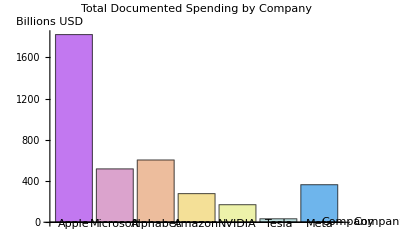

```mathematica
(* Get total spending by each company *)
totalByCompany = Association[
  Table[
    company -> Total[
      Select[
        (* Extract the investment amount from every record across all domains for the company *)
        Lookup[#, "investment_amount_billions_usd"] & /@ Flatten[Values[mag7Data[company]]],
        NumberQ (* Ensure we only sum numbers, ignoring Nulls *)
      ]
    ],
    {company, companies}
  ]
];

Print["Total Spending by Company (Billions USD):"];
BarChart[
  Values[totalByCompany],
  ChartLabels -> Keys[totalByCompany],
  ChartStyle -> "Pastel",
  ChartLegends -> None,
  AxesLabel -> {"Company", "Billions USD"},
  PlotLabel -> "Total Documented Spending by Company"
]
```

Top 10 Domains by Total Spending (Billions USD):

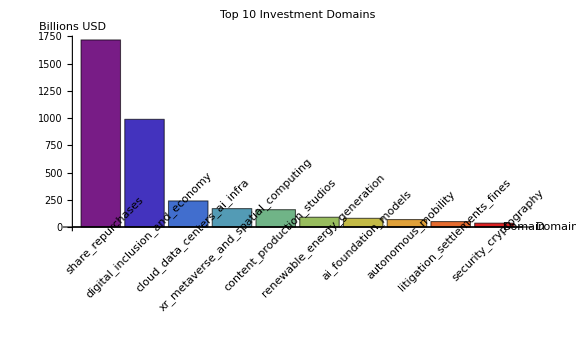

```mathematica
(* Create a summary table of top domains by spending *)
domainSpending = Association[
  Table[
    domain -> Total[
      Flatten[
        Table[
          (* Look up the domain for the company; default to empty list if missing *)
          With[{records = Lookup[mag7Data[company], domain, {}]},
            (* Extract amounts and filter for valid numbers *)
            Select[
              Lookup[#, "investment_amount_billions_usd"] & /@ records,
              NumberQ
            ]
          ],
          {company, companies}
        ]
      ]
    ],
    {domain, allDomains}
  ]
];

topDomains = TakeLargest[domainSpending, 10];
Print["Top 10 Domains by Total Spending (Billions USD):"];
BarChart[
  Values[topDomains],
  ChartLabels -> Placed[Keys[topDomains], Below, Rotate[#, 45 Degree] &],
  ChartStyle -> "Rainbow",
  AxesLabel -> {"Domain", "Billions USD"},
  PlotLabel -> "Top 10 Investment Domains",
  ImageSize -> Large
]
```

---
### Spending Records by Company
-   Expenditure ordered by greatest to least grouped by Company

#### Apple

```mathematica
(* Retrieve Apple's data *)
appleRawData = mag7Data["Apple"];

(* Flatten the nested structure and inject the raw 'Domain' key into each record *)
appleInvestments = Flatten[
  KeyValueMap[
    Function[{domainKey, recordsList},
      (* Just use the domainKey directly without modification *)
      Map[
        Append[#, "DisplayDomain" -> domainKey] &, 
        recordsList
      ]
    ],
    appleRawData
  ]
];

(* Calculate Total Spending by summing valid numeric amounts *)
appleTotalSpending = Total[
  Select[
    Lookup[appleInvestments, "investment_amount_billions_usd"], 
    NumberQ
  ]
];

Print["Apple's total investments: ", Length[appleInvestments], " records"];
Print["Apple's total spending: $", NumberForm[appleTotalSpending, {Infinity, 2}], " B"];

(* Show Apple's investments as a clean Dataset *)
Dataset[
  Query[All, <|
    "Domain" -> "DisplayDomain",
    "Year" -> "year",
    "Amount ($B)" -> "investment_amount_billions_usd",
    "Initiative" -> (If[ListQ[#initiatives], StringRiffle[#initiatives, ", "], #initiatives] &),
    "Notes" -> "notes"
  |>] @ appleInvestments
]
```

Apple's total investments: 74 records

Apple's total spending: $1822.22 B

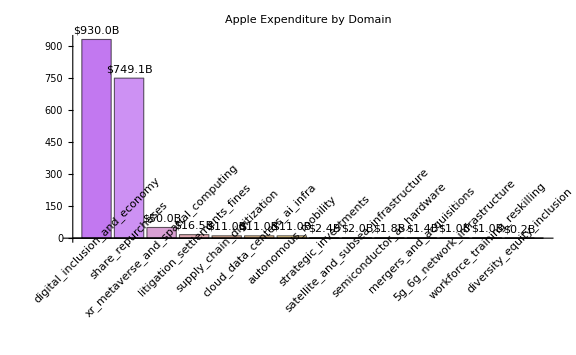

```mathematica
(* Import data *)
data = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];

(* Extract Apple data *)
appleData = data["Apple"];

(* Aggregate spending by domain (key) *)
domainSpending = Association[];
Do[
  total = Total[#["investment_amount_billions_usd"] & /@ appleData[domain]];
  If[total > 0, domainSpending[domain] = total],
  {domain, Keys[appleData]}
];

(* Sort by expenditure descending *)
sortedSpending = Sort[domainSpending, Greater];

(* Generate Bar Chart *)
BarChart[
  Values[sortedSpending],
  ChartLabels -> Placed[Keys[sortedSpending], Axis, Rotate[#, 45 Degree] &],
  PlotLabel -> Style["Apple Expenditure by Domain", 18, Bold],
  ChartStyle -> "Pastel",
  FrameLabel -> {None, "Investment (Billions USD)"},
  ImageSize -> Large,
  LabelingFunction -> (Placed[StringTemplate["$``B"][NumberForm[#, {Infinity, 1}]], Above] &)
]
```

#### Microsoft

```mathematica
(* Retrieve Microsoft's data *)
microsoftRawData = mag7Data["Microsoft"];

(* Flatten the nested structure and inject the raw 'Domain' key into each record *)
microsoftInvestments = Flatten[
  KeyValueMap[
    Function[{domainKey, recordsList},
      (* Just use the domainKey directly without modification *)
      Map[
        Append[#, "DisplayDomain" -> domainKey] &, 
        recordsList
      ]
    ],
    microsoftRawData
  ]
];

(* Calculate Total Spending by summing valid numeric amounts *)
microsoftTotalSpending = Total[
  Select[
    Lookup[microsoftInvestments, "investment_amount_billions_usd"], 
    NumberQ
  ]
];

Print["Microsoft's total investments: ", Length[microsoftInvestments], " records"];
Print["Microsoft's total spending: $", NumberForm[microsoftTotalSpending, {Infinity, 2}], " B"];

(* Show Microsoft's investments as a clean Dataset *)
Dataset[
  Query[All, <|
    "Domain" -> "DisplayDomain",
    "Year" -> "year",
    "Amount ($B)" -> "investment_amount_billions_usd",
    "Initiative" -> (If[ListQ[#initiatives], StringRiffle[#initiatives, ", "], #initiatives] &),
    "Notes" -> "notes"
  |>] @ microsoftInvestments
]
```

Microsoft's total investments: 95 records

Microsoft's total spending: $518.21 B

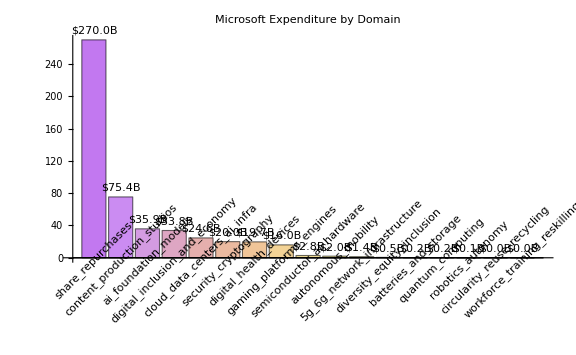

```mathematica
(* Import data *)
data = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];

(* Extract Microsoft data *)
microsoftData = data["Microsoft"];

(* Aggregate spending by domain (key) *)
domainSpending = Association[];
Do[
  total = Total[#["investment_amount_billions_usd"] & /@ microsoftData[domain]];
  If[total > 0, domainSpending[domain] = total],
  {domain, Keys[microsoftData]}
];

(* Sort by expenditure descending *)
sortedSpending = Sort[domainSpending, Greater];

(* Generate Bar Chart *)
BarChart[
  Values[sortedSpending],
  ChartLabels -> Placed[Keys[sortedSpending], Axis, Rotate[#, 45 Degree] &],
  PlotLabel -> Style["Microsoft Expenditure by Domain", 18, Bold],
  ChartStyle -> "Pastel",
  FrameLabel -> {None, "Investment (Billions USD)"},
  ImageSize -> Large,
  LabelingFunction -> (Placed[StringTemplate["$``B"][NumberForm[#, {Infinity, 1}]], Above] &)
]
```

#### Alphabet

```mathematica
(* Retrieve Alphabet's data *)
alphabetRawData = mag7Data["Alphabet"];

(* Flatten the nested structure and inject the raw 'Domain' key into each record *)
alphabetInvestments = Flatten[
  KeyValueMap[
    Function[{domainKey, recordsList},
      (* Just use the domainKey directly without modification *)
      Map[
        Append[#, "DisplayDomain" -> domainKey] &, 
        recordsList
      ]
    ],
    alphabetRawData
  ]
];

(* Calculate Total Spending by summing valid numeric amounts *)
alphabetTotalSpending = Total[
  Select[
    Lookup[alphabetInvestments, "investment_amount_billions_usd"], 
    NumberQ
  ]
];

Print["Alphabet's total investments: ", Length[alphabetInvestments], " records"];
Print["Alphabet's total spending: $", NumberForm[alphabetTotalSpending, {Infinity, 2}], " B"];

(* Show Alphabet's investments as a clean Dataset *)
Dataset[
  Query[All, <|
    "Domain" -> "DisplayDomain",
    "Year" -> "year",
    "Amount ($B)" -> "investment_amount_billions_usd",
    "Initiative" -> (If[ListQ[#initiatives], StringRiffle[#initiatives, ", "], #initiatives] &),
    "Notes" -> "notes"
  |>] @ alphabetInvestments
]
```

Alphabet's total investments: 79 records

Alphabet's total spending: $604.59 B

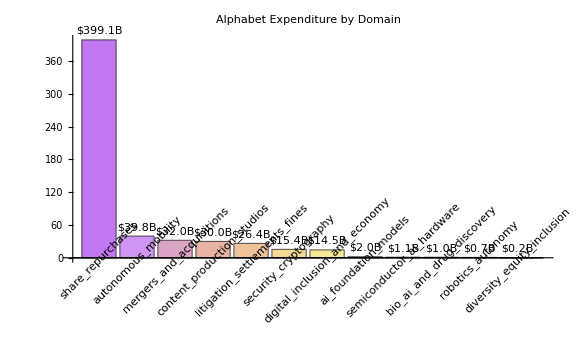

```mathematica
(* Import data *)
data = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];

(* Extract Alphabet data *)
alphabetData = data["Alphabet"];

(* Aggregate spending by domain (key) *)
domainSpending = Association[];
Do[
  total = Total[#["investment_amount_billions_usd"] & /@ alphabetData[domain]];
  If[total > 0, domainSpending[domain] = total],
  {domain, Keys[alphabetData]}
];

(* Sort by expenditure descending *)
sortedSpending = Sort[domainSpending, Greater];

(* Generate Bar Chart *)
BarChart[
  Values[sortedSpending],
  ChartLabels -> Placed[Keys[sortedSpending], Axis, Rotate[#, 45 Degree] &],
  PlotLabel -> Style["Alphabet Expenditure by Domain", 18, Bold],
  ChartStyle -> "Pastel",
  FrameLabel -> {None, "Investment (Billions USD)"},
  ImageSize -> Large,
  LabelingFunction -> (Placed[StringTemplate["$``B"][NumberForm[#, {Infinity, 1}]], Above] &)
]
```

#### Amazon

```mathematica
(* Retrieve Amazon's data *)
amazonRawData = mag7Data["Amazon"];

(* Flatten the nested structure and inject the raw 'Domain' key into each record *)
amazonInvestments = Flatten[
  KeyValueMap[
    Function[{domainKey, recordsList},
      (* Just use the domainKey directly without modification *)
      Map[
        Append[#, "DisplayDomain" -> domainKey] &, 
        recordsList
      ]
    ],
    amazonRawData
  ]
];

(* Calculate Total Spending by summing valid numeric amounts *)
amazonTotalSpending = Total[
  Select[
    Lookup[amazonInvestments, "investment_amount_billions_usd"], 
    NumberQ
  ]
];

Print["Amazon's total investments: ", Length[amazonInvestments], " records"];
Print["Amazon's total spending: $", NumberForm[amazonTotalSpending, {Infinity, 2}], " B"];

(* Show Amazon's investments as a clean Dataset *)
Dataset[
  Query[All, <|
    "Domain" -> "DisplayDomain",
    "Year" -> "year",
    "Amount ($B)" -> "investment_amount_billions_usd",
    "Initiative" -> (If[ListQ[#initiatives], StringRiffle[#initiatives, ", "], #initiatives] &),
    "Notes" -> "notes"
  |>] @ amazonInvestments
]
```

Amazon's total investments: 88 records

Amazon's total spending: $278.16 B

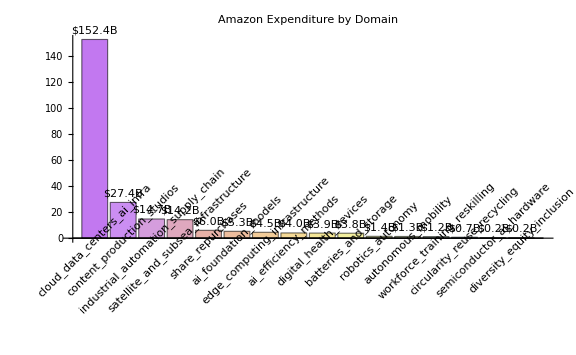

```mathematica
(* Import data *)
data = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];

(* Extract Amazon data *)
amazonData = data["Amazon"];

(* Aggregate spending by domain (key) *)
domainSpending = Association[];
Do[
  total = Total[#["investment_amount_billions_usd"] & /@ amazonData[domain]];
  If[total > 0, domainSpending[domain] = total],
  {domain, Keys[amazonData]}
];

(* Sort by expenditure descending *)
sortedSpending = Sort[domainSpending, Greater];

(* Generate Bar Chart *)
BarChart[
  Values[sortedSpending],
  ChartLabels -> Placed[Keys[sortedSpending], Axis, Rotate[#, 45 Degree] &],
  PlotLabel -> Style["Amazon Expenditure by Domain", 18, Bold],
  ChartStyle -> "Pastel",
  FrameLabel -> {None, "Investment (Billions USD)"},
  ImageSize -> Large,
  LabelingFunction -> (Placed[StringTemplate["$``B"][NumberForm[#, {Infinity, 1}]], Above] &)
]
```

#### Meta

```mathematica
(* Retrieve Meta's data *)
metaRawData = mag7Data["Meta"];

(* Flatten the nested structure and inject the raw 'Domain' key into each record *)
metaInvestments = Flatten[
  KeyValueMap[
    Function[{domainKey, recordsList},
      (* Just use the domainKey directly without modification *)
      Map[
        Append[#, "DisplayDomain" -> domainKey] &, 
        recordsList
      ]
    ],
    metaRawData
  ]
];

(* Calculate Total Spending by summing valid numeric amounts *)
metaTotalSpending = Total[
  Select[
    Lookup[metaInvestments, "investment_amount_billions_usd"], 
    NumberQ
  ]
];

Print["Meta's total investments: ", Length[metaInvestments], " records"];
Print["Meta's total spending: $", NumberForm[metaTotalSpending, {Infinity, 2}], " B"];

(* Show Meta's investments as a clean Dataset *)
Dataset[
  Query[All, <|
    "Domain" -> "DisplayDomain",
    "Year" -> "year",
    "Amount ($B)" -> "investment_amount_billions_usd",
    "Initiative" -> (If[ListQ[#initiatives], StringRiffle[#initiatives, ", "], #initiatives] &),
    "Notes" -> "notes"
  |>] @ metaInvestments
]
```

Meta's total investments: 82 records

Meta's total spending: $364.75 B

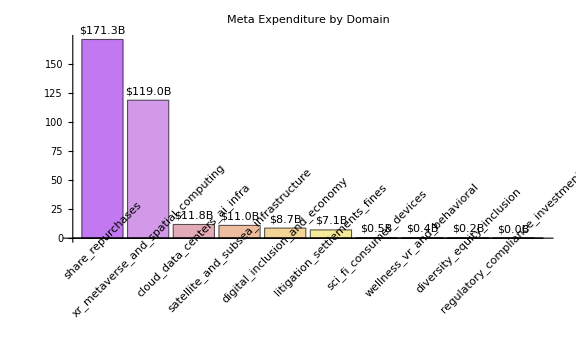

```mathematica
(* Import data *)
data = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];

(* Extract Meta data *)
metaData = data["Meta"];

(* Aggregate spending by domain (key) *)
domainSpending = Association[];
Do[
  total = Total[#["investment_amount_billions_usd"] & /@ metaData[domain]];
  If[total > 0, domainSpending[domain] = total],
  {domain, Keys[metaData]}
];

(* Sort by expenditure descending *)
sortedSpending = Sort[domainSpending, Greater];

(* Generate Bar Chart *)
BarChart[
  Values[sortedSpending],
  ChartLabels -> Placed[Keys[sortedSpending], Axis, Rotate[#, 45 Degree] &],
  PlotLabel -> Style["Meta Expenditure by Domain", 18, Bold],
  ChartStyle -> "Pastel",
  FrameLabel -> {None, "Investment (Billions USD)"},
  ImageSize -> Large,
  LabelingFunction -> (Placed[StringTemplate["$``B"][NumberForm[#, {Infinity, 1}]], Above] &)
]
```

#### NVIDIA

```mathematica
(* Retrieve Nvidia's data *)
nvidiaRawData = mag7Data["NVIDIA"];

(* Flatten the nested structure and inject the raw 'Domain' key into each record *)
nvidiaInvestments = Flatten[
  KeyValueMap[
    Function[{domainKey, recordsList},
      (* Just use the domainKey directly without modification *)
      Map[
        Append[#, "DisplayDomain" -> domainKey] &, 
        recordsList
      ]
    ],
    nvidiaRawData
  ]
];

(* Calculate Total Spending by summing valid numeric amounts *)
nvidiaTotalSpending = Total[
  Select[
    Lookup[nvidiaInvestments, "investment_amount_billions_usd"], 
    NumberQ
  ]
];

Print["Nvidia's total investments: ", Length[nvidiaInvestments], " records"];
Print["Nvidia's total spending: $", NumberForm[nvidiaTotalSpending, {Infinity, 2}], " B"];

(* Show Nvidia's investments as a clean Dataset *)
Dataset[
  Query[All, <|
    "Domain" -> "DisplayDomain",
    "Year" -> "year",
    "Amount ($B)" -> "investment_amount_billions_usd",
    "Initiative" -> (If[ListQ[#initiatives], StringRiffle[#initiatives, ", "], #initiatives] &),
    "Notes" -> "notes"
  |>] @ nvidiaInvestments
]
```

Nvidia's total investments: 49 records

Nvidia's total spending: $170.64 B

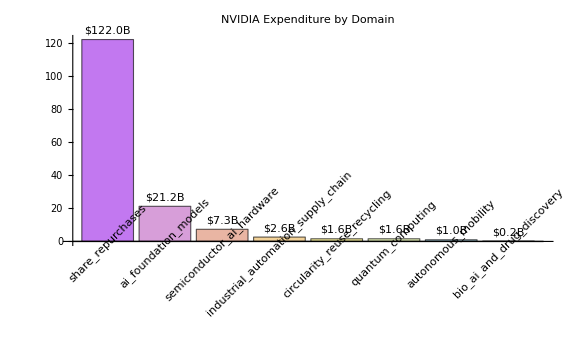

```mathematica
(* Import data *)
data = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];

(* Extract NVIDIA data *)
nvidiaData = data["NVIDIA"];

(* Aggregate spending by domain (key) *)
domainSpending = Association[];
Do[
  total = Total[#["investment_amount_billions_usd"] & /@ nvidiaData[domain]];
  If[total > 0, domainSpending[domain] = total],
  {domain, Keys[nvidiaData]}
];

(* Sort by expenditure descending *)
sortedSpending = Sort[domainSpending, Greater];

(* Generate Bar Chart *)
BarChart[
  Values[sortedSpending],
  ChartLabels -> Placed[Keys[sortedSpending], Axis, Rotate[#, 45 Degree] &],
  PlotLabel -> Style["NVIDIA Expenditure by Domain", 18, Bold],
  ChartStyle -> "Pastel",
  FrameLabel -> {None, "Investment (Billions USD)"},
  ImageSize -> Large,
  LabelingFunction -> (Placed[StringTemplate["$``B"][NumberForm[#, {Infinity, 1}]], Above] &)
]
```

#### Tesla

```mathematica
(* Retrieve Tesla's data *)
teslaRawData = mag7Data["Tesla"];

(* Flatten the nested structure and inject the raw 'Domain' key into each record *)
teslaInvestments = Flatten[
  KeyValueMap[
    Function[{domainKey, recordsList},
      (* Just use the domainKey directly without modification *)
      Map[
        Append[#, "DisplayDomain" -> domainKey] &, 
        recordsList
      ]
    ],
    teslaRawData
  ]
];

(* Calculate Total Spending by summing valid numeric amounts *)
teslaTotalSpending = Total[
  Select[
    Lookup[teslaInvestments, "investment_amount_billions_usd"], 
    NumberQ
  ]
];

Print["Tesla's total investments: ", Length[teslaInvestments], " records"];
Print["Tesla's total spending: $", NumberForm[teslaTotalSpending, {Infinity, 2}], " B"];

(* Show Tesla's investments as a clean Dataset *)
Dataset[
  Query[All, <|
    "Domain" -> "DisplayDomain",
    "Year" -> "year",
    "Amount ($B)" -> "investment_amount_billions_usd",
    "Initiative" -> (If[ListQ[#initiatives], StringRiffle[#initiatives, ", "], #initiatives] &),
    "Notes" -> "notes"
  |>] @ teslaInvestments
]
```

Tesla's total investments: 39 records

Tesla's total spending: $33.88 B

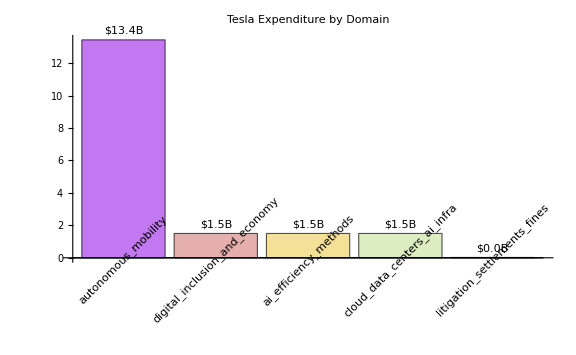

```mathematica
(* Import data *)
data = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];

(* Extract Tesla data *)
teslaData = data["Tesla"];

(* Aggregate spending by domain (key) *)
domainSpending = Association[];
Do[
  total = Total[#["investment_amount_billions_usd"] & /@ teslaData[domain]];
  If[total > 0, domainSpending[domain] = total],
  {domain, Keys[teslaData]}
];

(* Sort by expenditure descending *)
sortedSpending = Sort[domainSpending, Greater];

(* Generate Bar Chart *)
BarChart[
  Values[sortedSpending],
  ChartLabels -> Placed[Keys[sortedSpending], Axis, Rotate[#, 45 Degree] &],
  PlotLabel -> Style["Tesla Expenditure by Domain", 18, Bold],
  ChartStyle -> "Pastel",
  FrameLabel -> {None, "Investment (Billions USD)"},
  ImageSize -> Large,
  LabelingFunction -> (Placed[StringTemplate["$``B"][NumberForm[#, {Infinity, 1}]], Above] &)
]
```

---
### Cosine Similarity Correlation by spend_type Proportionality
-   Expenditure type proportionality by Company

```mathematica
(* Import data *)
data = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];
companies = Sort[Keys[data]];
n = Length[companies];

(* Build normalized spend-type distribution per company *)
getSpendingDistribution[company_] := Module[
  {typeTotals = Association[], total},
  Do[
    entries = data[company][category];
    If[ListQ[entries],
      Do[
        type = ToLowerCase[Lookup[entry, "spend_type", "other"]];
        amount = Lookup[entry, "investment_amount_billions_usd", 0.0];
        If[NumericQ[amount] && amount > 0,
          typeTotals[type] = Lookup[typeTotals, type, 0.0] + amount
        ],
        {entry, entries}
      ]
    ],
    {category, Keys[data[company]]}
  ];
  total = Total[Values[typeTotals]];
  If[total > 0, typeTotals/total, typeTotals]
];

distData = AssociationMap[getSpendingDistribution, companies];
allTypes = Sort[DeleteDuplicates[Flatten[Keys /@ Values[distData]]]];
vectors = Table[Lookup[distData[company], #, 0.0] & /@ allTypes, {company, companies}];

cosSim[v1_, v2_] := If[Norm[v1] > 0 && Norm[v2] > 0, v1.v2/(Norm[v1] Norm[v2]), 0.0];

similarityMatrix = Table[
  If[i == j, 1., cosSim[vectors[[i]], vectors[[j]]]],
  {i, n}, {j, n}
];

(* Reverse matrix rows manually for proper display *)
displayMatrix = Reverse[similarityMatrix];
displayCompanies = Reverse[companies];

(* Build tick specs *)
yTicks = Table[{i, displayCompanies[[i]]}, {i, n}];
xTicks = Table[{i, Rotate[companies[[i]], 90 Degree]}, {i, n}];

(* Custom color function: Purple for 1.0, Light Pink for 0.0 *)
pinkPurple = Blend[{RGBColor[0.5, 0, 0.5], RGBColor[1, 0.9, 0.95]}, #] &;

MatrixPlot[
  displayMatrix,
  ColorFunction -> pinkPurple,
  ColorFunctionScaling -> False,
  PlotRange -> {0, 1},
  FrameTicks -> {{yTicks, None}, {None, xTicks}},
  ImageSize -> Large,
  PlotLabel -> Style["Cosine Similarity of Spending Allocation", 16, Bold],
  PlotLegends -> BarLegend[
    {pinkPurple, {0, 1}}, 
    LegendLabel -> "Similarity"
  ],
  Epilog -> Flatten[
    Table[
      Text[
        Style[NumberForm[displayMatrix[[i, j]], {2, 2}], 10, Black],
        {j - 0.5, n - i + 0.5}
      ],
      {i, n}, {j, n}
    ], 1]
]
```

-Graphics-

---
### Spending Records by Company & Type

Total Spending by Category and Company (Billions USD):

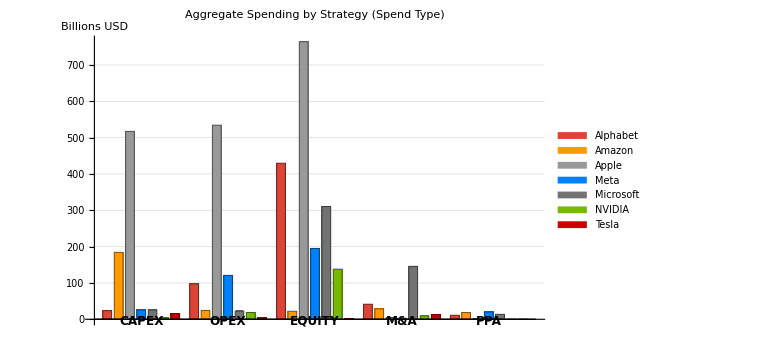

```mathematica
(* 1. Setup Companies and Colors *)
(* Ensure we get the company list from the loaded data *)
orderedCompanies = Sort[Keys[mag7Data]];

(* Define colors manually to ensure consistency *)
companyColors = <|
  "Apple" -> RGBColor["#999999"],      
  "Microsoft" -> RGBColor["#737373"],  
  "Alphabet" -> RGBColor["#DB4437"],   
  "Amazon" -> RGBColor["#FF9900"],     
  "Meta" -> RGBColor["#0081FB"],       
  "Tesla" -> RGBColor["#CC0000"],      
  "NVIDIA" -> RGBColor["#76B900"]      
|>;

(* Define the specific spend types to visualize *)
targetTypes = {"capex", "opex", "equity", "M&A", "ppa"};

(* 2. Flatten Data *)
(* Transform the nested JSON structure into a flat list of {Company, Type, Amount} *)
flatRecords = Flatten[
   Table[
    With[{comp = c},
     Map[
      {
        comp, 
        Lookup[#, "spend_type", "Other"], 
        (* Ensure amount is a number; default to 0.0 if missing *)
        N[Lookup[#, "investment_amount_billions_usd", 0.0]]
      } &,
      Flatten[Values[mag7Data[c]]]
     ]
    ],
    {c, orderedCompanies}
   ],
   1
];

(* Filter for valid numeric entries just in case *)
validRecords = Select[flatRecords, NumberQ[#[[3]]] &];

(* 3. Build Chart Matrix (Manual Aggregation) *)
(* We use Table/Select/Total to avoid GroupBy syntax issues *)
chartData = Table[
   Table[
    Total[
     Select[
      validRecords, 
      (#[[1]] == comp && #[[2]] == type) &
     ][[All, 3]]
    ],
    {comp, orderedCompanies}
   ],
   {type, targetTypes}
];

(* 4. Generate Plot *)
Print["Total Spending by Category and Company (Billions USD):"];

BarChart[
 chartData,
 ChartLayout -> "Grouped",
 
 (* Apply specific colors for each company in the group *)
 ChartStyle -> (companyColors[#] & /@ orderedCompanies),
 
 (* X-Axis Labels (Spend Types) *)
 ChartLabels -> {
   (Style[ToUpperCase[#], 12, Bold, FontFamily -> "Arial"] & /@ targetTypes), 
   None
 },
 
 (* Legend (Companies) *)
 ChartLegends -> Placed[
   SwatchLegend[
    companyColors[#] & /@ orderedCompanies,
    orderedCompanies,
    LegendLayout -> "Row"
   ],
   Below
 ],
 
 AxesLabel -> {None, "Billions USD"},
 PlotLabel -> Style["Aggregate Spending by Strategy (Spend Type)", 18, FontFamily -> "Arial"],
 ImageSize -> Large,
 ImagePadding -> {{60, 20}, {40, 30}},
 GridLines -> {None, Automatic}
]
```

---
## Data Visualization & Storytelling

-   Timeseries Visualizations, Datacenter Powerdraw Geo Visualization, Market Valuation

### Timeseries Visualization

#### 10-K, 10-Q, Decks

Loaded 297 records

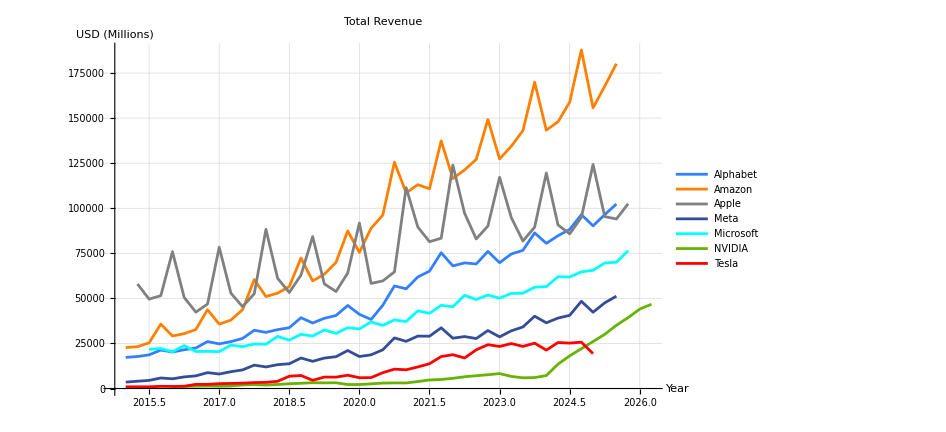
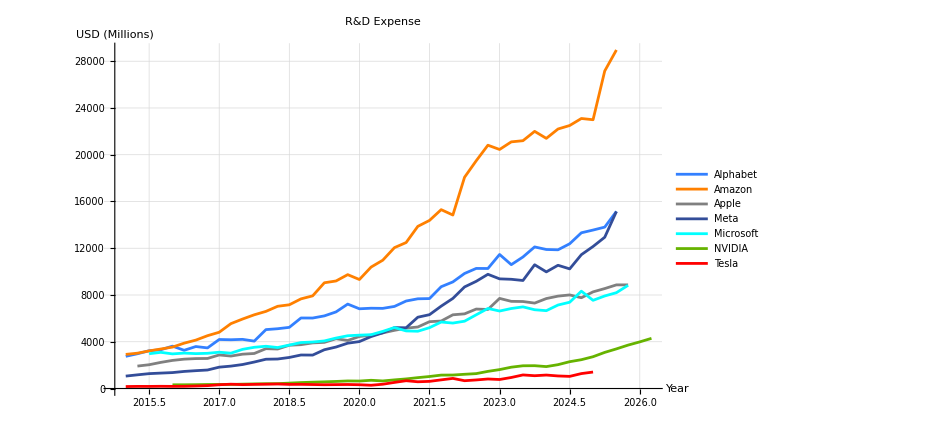
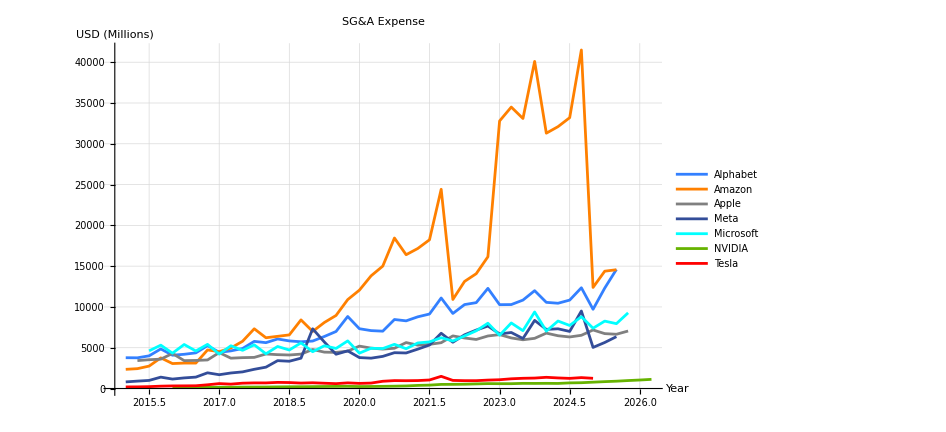
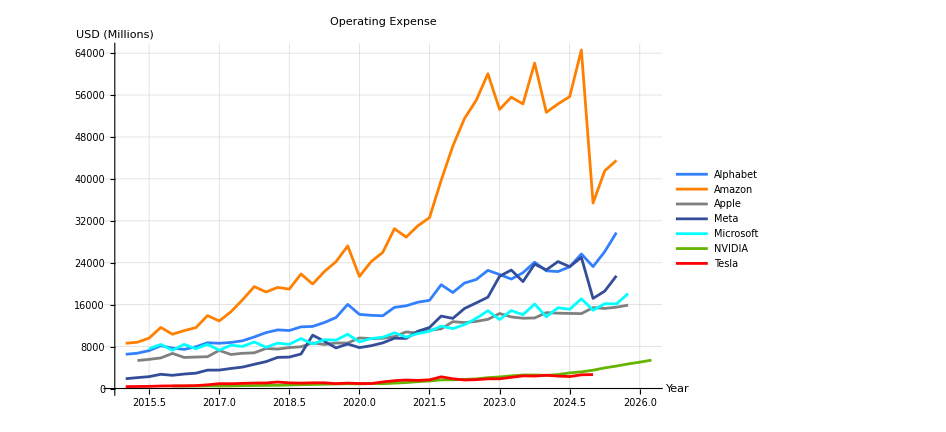
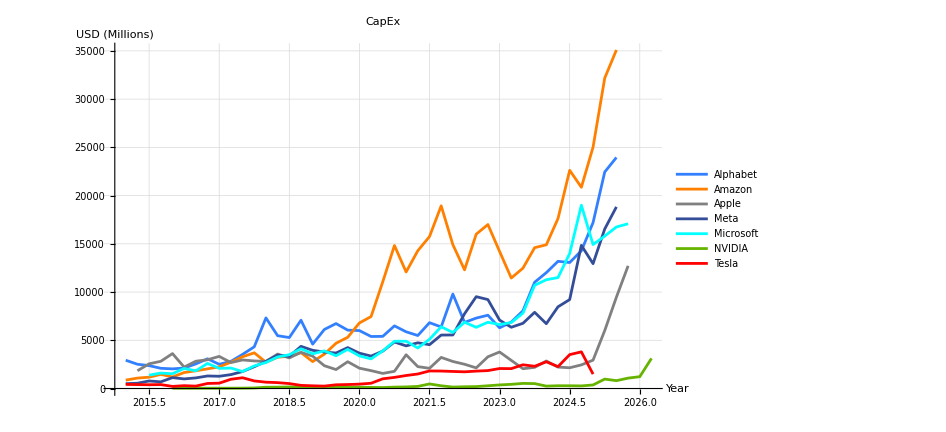

```mathematica
(* ====== 10-K/10-Q Financial Time Series ====== *)

(* Import JSON directly *)
raw = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/FY_10K_10Q.json", "RawJSON"];
records = raw["records"];

(* Verify data loaded *)
Print["Loaded ", Length[records], " records"];

(* Hard-coded company list *)
companiesList = {"Alphabet", "Amazon", "Apple", "Meta", "Microsoft", "NVIDIA", "Tesla"};

(* Metrics *)
metricKeys = {"revenue_total", "rd_expense", "sg_and_a_expense", "operating_expense_total", "capex_total"};
metricLabels = <|"revenue_total" -> "Total Revenue", "rd_expense" -> "R&D Expense", 
  "sg_and_a_expense" -> "SG&A Expense", "operating_expense_total" -> "Operating Expense", 
  "capex_total" -> "CapEx"|>;

(* Build series: filter records, extract x=year.quarter, y=value *)
buildSeries[metric_, company_] := Module[{filtered, pts},
  filtered = Select[records, #["company"] === company &];
  pts = Table[
    With[{yr = r["fiscal_year"], q = r["fiscal_quarter"], v = r[metric]},
      If[NumericQ[v], 
        {yr + (ToExpression[StringTake[q, -1]] - 1)/4, v}, 
        Nothing]
    ], {r, filtered}];
  SortBy[pts, First]
];

(* Colors for 7 companies *)
colors = {RGBColor[0.2, 0.5, 1], Orange, Gray, RGBColor[0.2, 0.3, 0.6], 
          Cyan, RGBColor[0.4, 0.7, 0], Red};

(* Plot function *)
makePlot[metric_] := Module[{allSeries},
  allSeries = Table[buildSeries[metric, c], {c, companiesList}];
  ListLinePlot[allSeries,
    PlotLabel -> Style[metricLabels[metric], Bold, 14],
    PlotLegends -> Placed[companiesList, Right],
    PlotStyle -> colors,
    ImageSize -> {700, 300},
    AxesLabel -> {"Year", "USD (Millions)"},
    GridLines -> Automatic,
    PlotRange -> All,
    Joined -> True
  ]
];

(* Generate all 5 plots *)
Column[Table[makePlot[m], {m, metricKeys}], Spacings -> 2]
```

### Geo Visualization of Datacenter Locations by Company

```mathematica
(* 1. Import the Data *)
(* Update path as needed *)
datacenters = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/datacenters.json", "RawJSON"];

(* 2. Extract and Flatten the Data *)
(* Now extracting 'power_draw_mw' as well *)
rawLocations = Flatten[
   Table[
    With[{companyData = datacenters[company]},
     Table[
      With[{site = companyData[key]},
       <|
        "Company" -> company,
        "Address" -> StringRiffle[DeleteCases[{site["city"], site["state"], site["country"]}, Nothing | Null | "N/A"], ", "],
        "Name" -> site["location_name"],
        "Power" -> site["power_draw_mw"]
       |>
       ],
      {key, Keys[companyData]}
      ]
     ],
    {company, Keys[datacenters]}
    ],
   1];

(* 3. Geocode the Addresses *)
uniqueAddresses = DeleteDuplicates[rawLocations[[All, "Address"]]];

Print["Geocoding " <> ToString[Length[uniqueAddresses]] <> " unique locations..."];
(* Note: Requires internet connection *)
geoPositions = AssociationThread[
   uniqueAddresses -> Interpreter["Location"][uniqueAddresses]
   ];

(* 4. Define Styling and Sizing Logic *)
companyColors = <|
   "Alphabet" -> RGBColor["#DB4437"],
   "Amazon" -> RGBColor["#FF9900"],
   "Microsoft" -> RGBColor["#00A4EF"],
   "Meta" -> RGBColor["#0668E1"],
   "Apple" -> RGBColor["#A2AAAD"],
   "Tesla" -> RGBColor["#cc0000"],
   "NVIDIA" -> RGBColor["#76B900"]
   |>;

(* Determine Max Power for scaling (ignoring Nulls) *)
maxPower = Max[Select[rawLocations[[All, "Power"]], NumericQ]];

(* Function to calculate point size *)
(* Uses Square Root scaling so massive 5GW outliers don't hide everything else *)
(* Default size (0.01) for Null values *)
calcPointSize[power_] := If[
   NumericQ[power], 
   0.01 + 0.025 * (Sqrt[power] / Sqrt[maxPower]), 
   0.01
   ];

(* 5. Construct Plot Primitives *)
plotPrimitives = Table[
   With[{
     pos = geoPositions[item["Address"]],
     color = Lookup[companyColors, item["Company"], Black],
     size = calcPointSize[item["Power"]],
     label = item["Name"],
     pwrLabel = If[NumericQ[item["Power"]], ToString[item["Power"]] <> " MW", "Unknown MW"]
     },
    (* Only plot if geocoding succeeded *)
    If[Head[pos] === GeoPosition,
     {
      color,
      PointSize[size],
      Tooltip[
       Point[pos], 
       Column[{Style[label, Bold], item["Company"], pwrLabel}]
      ]
     },
     Nothing
     ]
    ],
   {item, rawLocations}
   ];

(* 6. Generate the Plot with Legend *)
Legended[
 GeoGraphics[
  {
   Opacity[0.75],
   plotPrimitives
  },
  GeoBackground -> "VectorMinimal",
  GeoProjection -> "Robinson",
  ImageSize -> 1000,
  GeoRange -> "World",
  PlotLabel -> Style["Hyperscale Data Center Locations\n(Sized by Power Draw)", 20, FontFamily -> "Helvetica"]
  ],
 Placed[
  SwatchLegend[
   Values[companyColors],
   Keys[companyColors],
   LegendLayout -> "Row",
   LegendLabel -> "Company"
   ],
  Below
  ]
 ]
```

Geocoding 73 unique locations...

-Graphics-

### Price Visualization Market Valuation

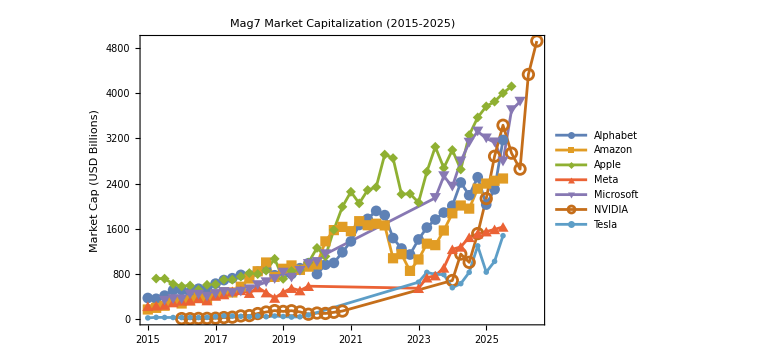
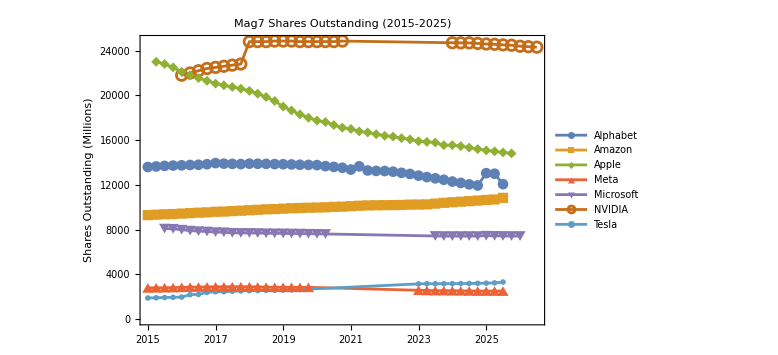
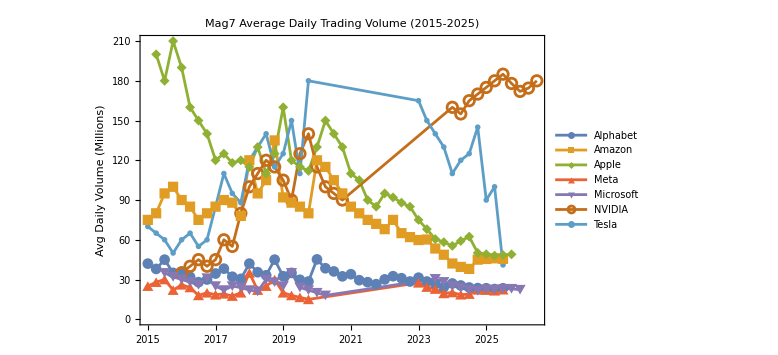

```mathematica
(* Import market valuation data *)
data = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/market_valuation.json", "RawJSON"];
records = data["records"];

(* Convert quarter to date *)
quarterToDate[year_, quarter_] := 
  DateObject[{year, Switch[quarter, "Q1", 1, "Q2", 4, "Q3", 7, "Q4", 10], 1}];

(* Define Mag7 companies *)
mag7 = {"Alphabet", "Amazon", "Apple", "Meta", "Microsoft", "NVIDIA", "Tesla"};

(* Color palette for companies *)
colors = Association[Thread[mag7 -> ColorData[97, "ColorList"][[;; 7]]]];

(* Extract time series for a given metric and company *)
extractSeries[company_, metric_] := Module[{companyData, points},
  companyData = Select[records, #["company"] == company &];
  points = {quarterToDate[#["fiscal_year"], #["fiscal_quarter"]], #[metric]} & /@ companyData;
  points = Select[points, NumericQ[Last[#]] &];
  TimeSeries[SortBy[points, First]]
];

(* Create plot for a single metric *)
metricPlot[metric_, title_, yLabel_] := Module[{series},
  series = Table[
    Legended[
      extractSeries[company, metric], 
      Placed[company, After]
    ],
    {company, mag7}
  ];
  DateListPlot[
    Table[extractSeries[company, metric], {company, mag7}],
    PlotLegends -> mag7,
    PlotStyle -> (colors /@ mag7),
    PlotRange -> All,
    ImageSize -> Large,
    PlotLabel -> Style[title, Bold, 16],
    FrameLabel -> {None, yLabel},
    Frame -> True,
    GridLines -> Automatic,
    DateTicksFormat -> {"Year"},
    Joined -> True,
    PlotMarkers -> Automatic
  ]
];

(* Generate all three visualizations *)
Grid[{
  {metricPlot["market_cap_usd", "Mag7 Market Capitalization (2015-2025)", "Market Cap (USD Billions)"]},
  {metricPlot["shares_outstanding_m", "Mag7 Shares Outstanding (2015-2025)", "Shares Outstanding (Millions)"]},
  {metricPlot["avg_daily_volume_m", "Mag7 Average Daily Trading Volume (2015-2025)", "Avg Daily Volume (Millions)"]}
}, Spacings -> {0, 2}]
```

---
## Sustainability Deep Dive
-   Total energy consumption by year (GWh)
-   Cummulative energy consumption
-   Total / Cumulative cost of energy consumed ($85K/GWh)
-   Total / Cumulative renewable energy expenditure by year
-   Renewable energy expenditure / Total cost of electricity

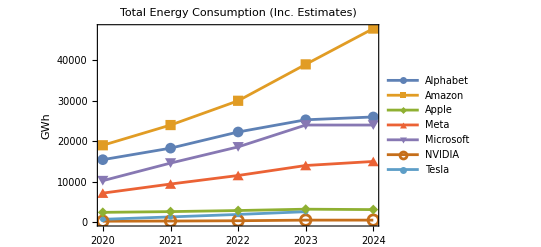
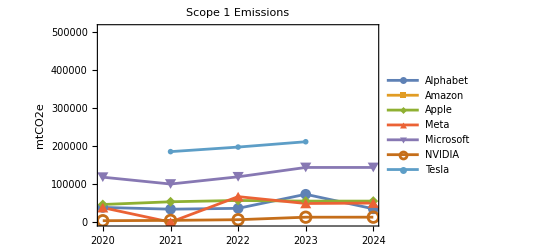
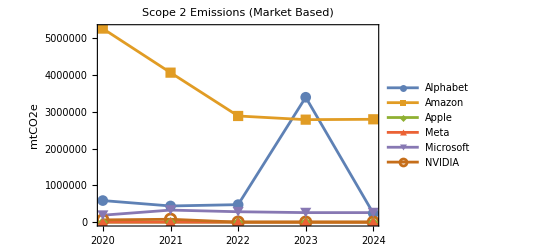
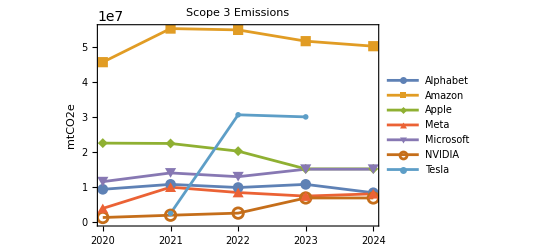
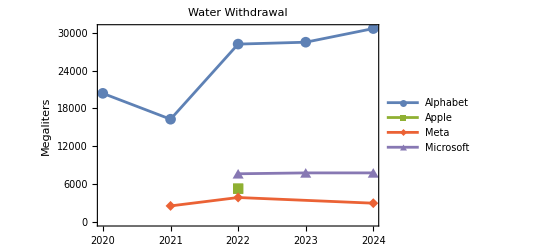
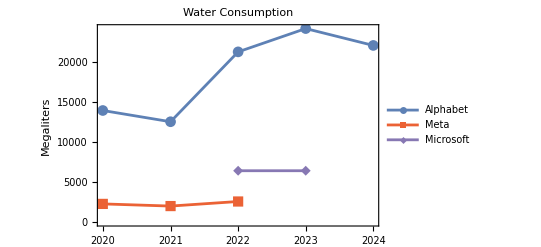
-Graphics- | 
-Graphics- | -Graphics-
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
(* Import ESG data *)
data = Import["/Users/shlinky/Documents/MSBA/Storytelling/!!BDI_FINAL/ESG.json", "RawJSON"];
companiesData = data["companies"];
mag7 = Sort[Keys[companiesData]];

(* Assign consistent colors to companies *)
colors = Association[Thread[mag7 -> ColorData[97, "ColorList"][[;; Length[mag7]]]]];

(* Helper function to extract time series with estimation fallback *)
getMetricSeries[company_, category_, field_, scaleFactor_: 1] := Module[
   {years, yearData, val, scope2, timePairs},
   years = Sort[Keys[companiesData[company]]];
   
   timePairs = Table[
     yearData = First[companiesData[company][year], Nothing];
     If[yearData === Nothing, Nothing,
      
      (* Attempt to get direct value *)
      val = yearData[category][field];
      
      (* Fallback Logic for Energy Consumption if missing *)
      If[(MissingQ[val] || val === Null) && field === "total_consumption_mwh",
        scope2 = yearData["emissions_mtco2e"]["scope_2_location_based"];
        If[NumericQ[scope2],
         (* Estimate MWh from Scope 2 Location Based Emissions *)
         (* using approx grid intensity ~0.385 tonnes CO2/MWh *)
         val = scope2 / 0.385;
        ]
      ];

      If[NumericQ[val],
       {DateObject[{ToExpression[year]}], val * scaleFactor},
       Nothing
       ]
      ],
     {year, years}
     ];
     
   If[Length[timePairs] > 0, TimeSeries[timePairs], Nothing]
   ];

(* Robust plotting function *)
createPlot[category_, field_, title_, yLabel_, scale_: 1] := Module[
   {seriesData, companiesWithData, seriesList, colorsList, s},
   
   (* Safely build list of {company, series} pairs *)
   seriesData = {};
   Do[
    s = getMetricSeries[company, category, field, scale];
    If[s =!= Nothing, AppendTo[seriesData, {company, s}]],
    {company, mag7}
   ];
   
   If[Length[seriesData] == 0, 
    Return[Graphics[{Text["No Data", {0, 0}]}, Frame -> True, PlotLabel -> title, ImageSize -> 400]]];

   companiesWithData = seriesData[[All, 1]];
   seriesList = seriesData[[All, 2]];
   colorsList = colors /@ companiesWithData;
   
   DateListPlot[seriesList,
    PlotLabel -> Style[title, 14, Bold],
    FrameLabel -> {None, yLabel},
    PlotStyle -> colorsList,
    PlotLegends -> Placed[companiesWithData, Right],
    ImageSize -> 400,
    Frame -> True,
    GridLines -> Automatic,
    PlotMarkers -> Automatic,
    Joined -> True
    ]
   ];

(* 1. Energy Consumption Plot (MWh converted to GWh) *)
(* Note: Includes fallback estimation for missing data *)
energyPlot = createPlot["energy_consumption", "total_consumption_mwh", 
   "Total Energy Consumption (Inc. Estimates)", "GWh", 1/1000.0];

(* 2. Emissions Plots *)
scope1 = createPlot["emissions_mtco2e", "scope_1", 
   "Scope 1 Emissions", "mtCO2e"];
scope2 = createPlot["emissions_mtco2e", "scope_2_market_based", 
   "Scope 2 Emissions (Market Based)", "mtCO2e"];
scope3 = createPlot["emissions_mtco2e", "scope_3_total", 
   "Scope 3 Emissions", "mtCO2e"];

(* 3. Water Plots *)
waterWithdrawal = createPlot["water_metrics", "withdrawal", 
   "Water Withdrawal", "Megaliters"];
waterConsumption = createPlot["water_metrics", "consumption", 
   "Water Consumption", "Megaliters"];

(* Arrange all plots in a grid *)
Grid[{
  {energyPlot, SpanFromLeft},
  {scope1, scope2},
  {scope3, SpanFromLeft},
  {waterWithdrawal, waterConsumption}
}, Spacings -> {1, 2}, Frame -> All]
```

#### Total Rollup Renewable Energy Expenditure

Lookup::invrl: The argument Null is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

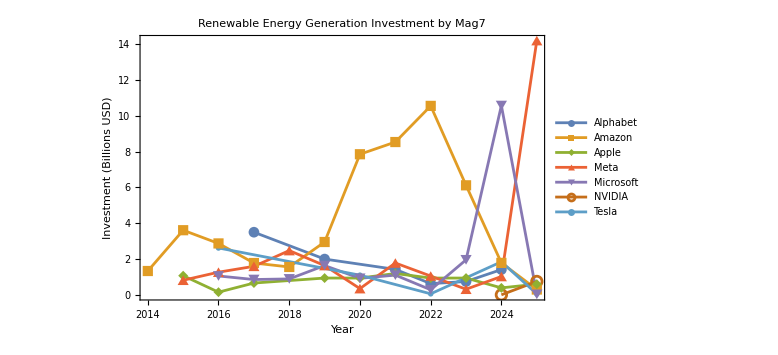

```mathematica
(* Import spending data *)
spendingData = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];
mag7Companies = Sort[Keys[spendingData]];

(* Assign colors to companies *)
colors = Association[Thread[mag7Companies -> ColorData[97, "ColorList"][[;; Length[mag7Companies]]]]];

(* Helper to process entries into year-value pairs *)
processEntry[entry_] := Module[
   {amount, year, tf, start, end, duration, yearlyAmount},
   amount = Lookup[entry, "investment_amount_billions_usd", 0.0];
   If[! NumericQ[amount], amount = 0.0];
   If[amount == 0.0, Return[{}]]; (* Skip zero amounts *)
   
   year = entry["year"];
   tf = entry["timeframe"];
   
   (* Case 1: Specific year is available *)
   If[NumericQ[year],
    Return[{{IntegerPart[year], amount}}]
    ];
   
   (* Case 2: No specific year, but timeframe exists *)
   If[(MissingQ[year] || year === Null) && ! MissingQ[tf] && ListQ[tf] == False,
    start = Lookup[tf, "start", Null];
    end = Lookup[tf, "end", Null];
    
    If[NumericQ[start] && NumericQ[end] && end >= start,
     duration = IntegerPart[end - start + 1];
     yearlyAmount = amount / duration;
     Return[Table[{y, yearlyAmount}, {y, IntegerPart[start], IntegerPart[end]}]],
     
     (* Fallback: use start or end if one exists *)
     If[NumericQ[start], Return[{{IntegerPart[start], amount}}]];
     If[NumericQ[end], Return[{{IntegerPart[end], amount}}]];
     ]
    ];
   
   Return[{}] (* No valid date found *)
   ];

(* Extract renewable energy generation spending by company and year *)
getRenewableEnergySeries[company_] := Module[
  {allCategories, renewableEntries, flattenedData, yearlyTotals, validPoints},
  
  allCategories = spendingData[company];
  renewableEntries = {};
  
  (* 1. Get entries from specific category *)
  If[KeyExistsQ[allCategories, "renewable_energy_generation"],
    renewableEntries = Join[renewableEntries, allCategories["renewable_energy_generation"]]
  ];
  
  (* 2. Search other categories for type match *)
  Do[
    If[ListQ[allCategories[category]],
      Do[
        If[KeyExistsQ[entry, "type"] && entry["type"] == "renewable_energy_generation",
          AppendTo[renewableEntries, entry]
        ],
        {entry, allCategories[category]}
      ]
    ],
    {category, Keys[allCategories]}
  ];
  
  (* Process all entries to handle multi-year splits *)
  flattenedData = Flatten[processEntry /@ renewableEntries, 1];
  
  If[Length[flattenedData] == 0, Return[Nothing]];
  
  (* Group by year and sum investment amounts *)
  yearlyTotals = GroupBy[flattenedData, First -> Last, Total];
  
  (* Convert to time series format *)
  validPoints = {DateObject[{#}], yearlyTotals[#]} & /@ Sort[Keys[yearlyTotals]];
  
  If[Length[validPoints] > 0, TimeSeries[validPoints], Nothing]
];

(* Build series and metadata for companies with renewable energy data *)
seriesData = {};
Do[
  series = getRenewableEnergySeries[company];
  If[series =!= Nothing, AppendTo[seriesData, {company, series}]],
  {company, mag7Companies}
];

If[Length[seriesData] == 0,
  Print["No renewable energy generation data found"];
  Abort[]
];

(* Extract companies and series *)
companiesWithData = seriesData[[All, 1]];
seriesList = seriesData[[All, 2]];
colorsList = colors /@ companiesWithData;

(* Create the plot *)
DateListPlot[seriesList,
  PlotLabel -> Style["Renewable Energy Generation Investment by Mag7", 16, Bold],
  FrameLabel -> {"Year", "Investment (Billions USD)"},
  PlotStyle -> colorsList,
  PlotLegends -> Placed[companiesWithData, Right],
  ImageSize -> Large,
  Frame -> True,
  GridLines -> Automatic,
  PlotMarkers -> Automatic,
  Joined -> True,
  PlotRange -> All,
  DateTicksFormat -> {"Year"}
]
```

Lookup::invrl: The argument Null is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

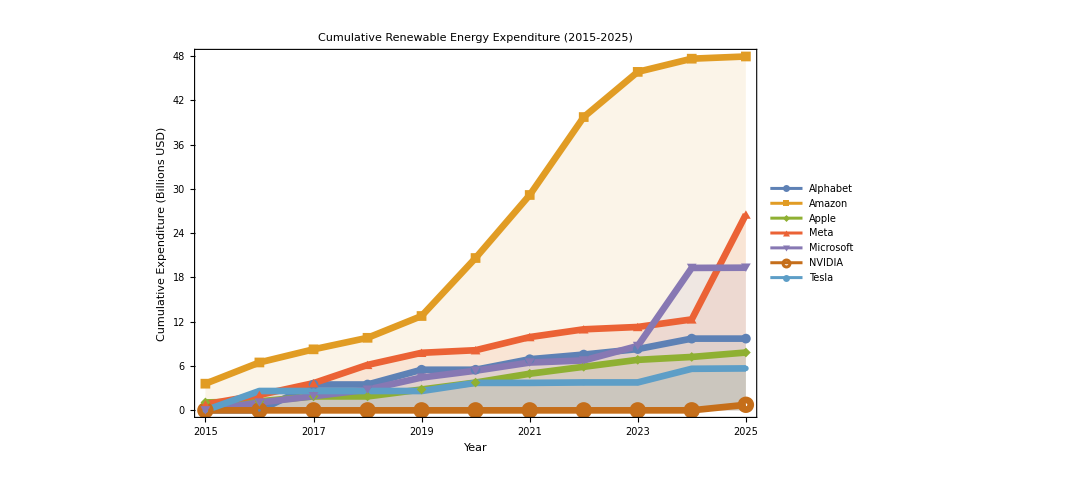

```mathematica
(* Import spending data *)
spendingData = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];
mag7Companies = Sort[Keys[spendingData]];

(* Assign colors to companies *)
colors = Association[Thread[mag7Companies -> ColorData[97, "ColorList"][[;; Length[mag7Companies]]]]];

(* Define full analysis range *)
yearsRange = Range[2015, 2025];

(* Helper to process entries into year-value pairs *)
processEntry[entry_] := Module[
   {amount, year, tf, start, end, duration, yearlyAmount},
   amount = Lookup[entry, "investment_amount_billions_usd", 0.0];
   If[! NumericQ[amount], amount = 0.0];
   If[amount == 0.0, Return[{}]]; (* Skip zero amounts *)
   
   year = entry["year"];
   tf = entry["timeframe"];
   
   (* Case 1: Specific year is available *)
   If[NumericQ[year],
    Return[{{IntegerPart[year], amount}}]
    ];
   
   (* Case 2: No specific year, but timeframe exists *)
   If[(MissingQ[year] || year === Null) && ! MissingQ[tf] && ListQ[tf] == False,
    start = Lookup[tf, "start", Null];
    end = Lookup[tf, "end", Null];
    
    If[NumericQ[start] && NumericQ[end] && end >= start,
     duration = IntegerPart[end - start + 1];
     yearlyAmount = amount / duration;
     Return[Table[{y, yearlyAmount}, {y, IntegerPart[start], IntegerPart[end]}]],
     
     (* Fallback: use start or end if one exists *)
     If[NumericQ[start], Return[{{IntegerPart[start], amount}}]];
     If[NumericQ[end], Return[{{IntegerPart[end], amount}}]];
     ]
    ];
   
   Return[{}] (* No valid date found *)
   ];

(* Extract cumulative renewable energy series *)
getCumulativeRenewableSeries[company_] := Module[
  {allCategories, renewableEntries, flattenedData, yearlyTotals, timePairs, timeSeries, cumulativeSeries},
  
  allCategories = spendingData[company];
  renewableEntries = {};
  
  (* 1. Get entries from specific category *)
  If[KeyExistsQ[allCategories, "renewable_energy_generation"],
    renewableEntries = Join[renewableEntries, allCategories["renewable_energy_generation"]]
  ];
  
  (* 2. Search other categories for type match *)
  Do[
    If[ListQ[allCategories[category]],
      Do[
        If[KeyExistsQ[entry, "type"] && entry["type"] == "renewable_energy_generation",
          AppendTo[renewableEntries, entry]
        ],
        {entry, allCategories[category]}
      ]
    ],
    {category, Keys[allCategories]}
  ];
  
  (* Process all entries to handle multi-year splits *)
  flattenedData = Flatten[processEntry /@ renewableEntries, 1];
  
  If[Length[flattenedData] == 0, Return[Nothing]];
  
  (* Sum by year *)
  yearlyTotals = GroupBy[flattenedData, First -> Last, Total];
  
  (* Build continuous timeline 2015-2025 *)
  timePairs = Table[
    {DateObject[{y}], Lookup[yearlyTotals, y, 0.0]}, 
    {y, yearsRange}
  ];
  
  (* Accumulate values *)
  timeSeries = TimeSeries[timePairs];
  cumulativeSeries = TimeSeries[
    Transpose[{
      timeSeries["Dates"], 
      Accumulate[timeSeries["Values"]]
    }]
  ];
  
  cumulativeSeries
];

(* Build plot data *)
seriesData = {};
Do[
  series = getCumulativeRenewableSeries[company];
  If[series =!= Nothing, AppendTo[seriesData, {company, series}]],
  {company, mag7Companies}
];

If[Length[seriesData] == 0,
  Print["No data found matching criteria."];
  Abort[];
];

(* Extract for plotting *)
companiesWithData = seriesData[[All, 1]];
seriesList = seriesData[[All, 2]];
colorsList = colors /@ companiesWithData;

(* Generate Plot *)
DateListPlot[seriesList,
  PlotLabel -> Style["Cumulative Renewable Energy Expenditure (2015-2025)", 16, Bold],
  FrameLabel -> {"Year", "Cumulative Expenditure (Billions USD)"},
  PlotStyle -> (Directive[#, Thickness[0.006]] & /@ colorsList),
  PlotLegends -> Placed[companiesWithData, Right],
  ImageSize -> 800,
  Frame -> True,
  GridLines -> Automatic,
  PlotMarkers -> {Automatic, 10},
  Joined -> True,
  PlotRange -> {All, All},
  DateTicksFormat -> {"Year"},
  Filling -> Axis,
  FillingStyle -> Opacity[0.1]
]
```

#### Price of 1 GWh of Electricity in the US on average - Industrial/Data Center Rates ($85k Mean) - The 68% Range: $60,000 to $110,000 per GWh

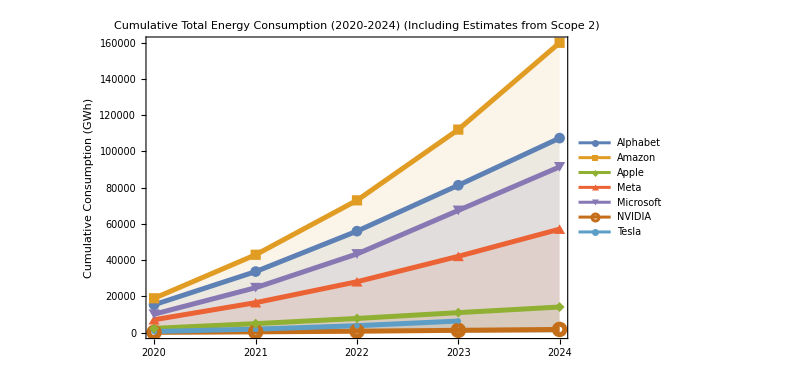

```mathematica
(* Function to compute cumulative energy consumption series *)
getCumulativeEnergySeries[company_] := Module[
   {years, yearData, val, scope2, timePairs, timeSeries, cumulativeSeries},
   years = Sort[Keys[companiesData[company]]];
   
   (* Extract yearly values *)
   timePairs = Table[
     yearData = First[companiesData[company][year], Nothing];
     If[yearData === Nothing, Nothing,
      (* Try direct energy consumption first *)
      val = yearData["energy_consumption"]["total_consumption_mwh"];
      
      (* If missing, estimate from Scope 2 (Location Based) *)
      If[MissingQ[val] || val === Null,
       scope2 = yearData["emissions_mtco2e"]["scope_2_location_based"];
       If[NumericQ[scope2],
        (* Estimate: MWh = Tonnes CO2 / 0.385 (approx global grid intensity factor) *)
        val = scope2 / 0.385; 
        ,
        val = Null
        ]
       ];

      If[NumericQ[val],
       {DateObject[{ToExpression[year]}], val * 1/1000.0} (* Convert MWh to GWh *)
       ,
       Nothing
       ]
      ],
     {year, years}
     ];
   
   If[Length[timePairs] == 0, Return[Nothing]];

   (* Create time series and accumulate *)
   timeSeries = TimeSeries[timePairs];
   cumulativeSeries = TimeSeries[
     Transpose[{
       timeSeries["Dates"],
       Accumulate[timeSeries["Values"]]
     }]
   ];
   
   cumulativeSeries
   ];

(* Generate Plot Data *)
cumulativeEnergyData = {};
Do[
  s = getCumulativeEnergySeries[company];
  If[s =!= Nothing, AppendTo[cumulativeEnergyData, {company, s}]],
  {company, mag7}
  ];

(* Create Cumulative Plot *)
If[Length[cumulativeEnergyData] > 0,
 companiesWithData = cumulativeEnergyData[[All, 1]];
 seriesList = cumulativeEnergyData[[All, 2]];
 colorsList = colors /@ companiesWithData;

 DateListPlot[seriesList,
  PlotLabel -> Style["Cumulative Total Energy Consumption (2020-2024)\n(Including Estimates from Scope 2)", 16, Bold],
  FrameLabel -> {None, "Cumulative Consumption (GWh)"},
  PlotStyle -> (Directive[#, Thickness[0.006]] & /@ colorsList),
  PlotLegends -> Placed[companiesWithData, Right],
  ImageSize -> 600,
  Frame -> True,
  GridLines -> Automatic,
  PlotMarkers -> Automatic,
  Joined -> True,
  PlotRange -> All,
  Filling -> Axis,
  FillingStyle -> Opacity[0.1]
  ],
 Print["No energy consumption data found."]
 ]
```

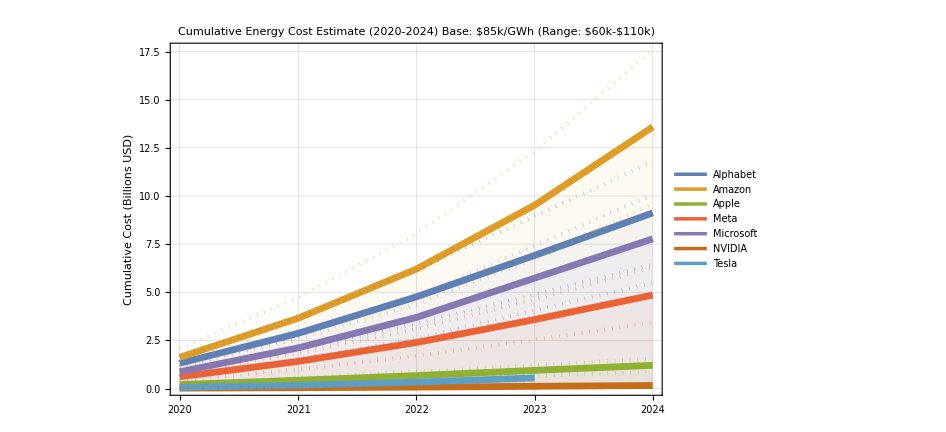

```mathematica
(* Function to compute cost series *)
(* pricePerGWh: Cost in USD per GWh *)
(* scale: scaling factor to get to Billions (10^-9) *)
getCostSeries[company_, pricePerGWh_] := Module[
   {energySeries, values, dates},
   energySeries = getCumulativeEnergySeries[company]; (* Relies on previous function *)
   If[energySeries === Nothing, Return[Nothing]];
   
   dates = energySeries["Dates"];
   values = energySeries["Values"] * pricePerGWh * 10^-9; (* Convert to Billions USD *)
   
   TimeSeries[Transpose[{dates, values}]]
   ];

(* Generate Main Cost Data ($85k/GWh) *)
costDataMain = {};
costDataLow = {};
costDataHigh = {};

Do[
  sMain = getCostSeries[company, 85000];
  sLow = getCostSeries[company, 60000];
  sHigh = getCostSeries[company, 110000];
  
  If[sMain =!= Nothing,
   AppendTo[costDataMain, {company, sMain}];
   AppendTo[costDataLow, sLow];
   AppendTo[costDataHigh, sHigh];
   ],
  {company, mag7}
  ];

If[Length[costDataMain] > 0,
 companiesWithData = costDataMain[[All, 1]];
 seriesList = costDataMain[[All, 2]];
 colorsList = colors /@ companiesWithData;

 (* Combine all plots *)
 Show[
  (* Main Lines ($85k) *)
  DateListPlot[seriesList,
   PlotStyle -> (Directive[#, Thickness[0.007]] & /@ colorsList),
   PlotLegends -> Placed[companiesWithData, Right],
   Filling -> Axis,
   FillingStyle -> Opacity[0.05]
   ],
  
  (* Lower Bound Lines ($60k) *)
  DateListPlot[costDataLow,
   PlotStyle -> (Directive[#, Dotted, Opacity[0.5], Thickness[0.004]] & /@ colorsList)
   ],
  
  (* Upper Bound Lines ($110k) *)
  DateListPlot[costDataHigh,
   PlotStyle -> (Directive[#, Dotted, Opacity[0.5], Thickness[0.004]] & /@ colorsList)
   ],

  PlotLabel -> Style["Cumulative Energy Cost Estimate (2020-2024)\nBase: $85k/GWh (Range: $60k-$110k)", 16, Bold],
  FrameLabel -> {None, "Cumulative Cost (Billions USD)"},
  Frame -> True,
  GridLines -> Automatic,
  ImageSize -> 700,
  PlotRange -> All
  ],
 Print["No data available for cost plot."]
 ]
```

#### Renewable Expenditure to Total Energy Expenditure Ratio by Year - Industrial/Data Center Rates ($85k Mean) - CapEx and OpEx Expenditures on Renewable Energy Generation divided by the term length of the contract to get yearly expenditure

```mathematica
(* --- ROBUST DATA EXTRACTION WITH FULL IMPUTATION --- *)

getYearlyEnergyData[company_] := Module[
   {compData, allYears, rawData, lastVal, yearData, currentVal, isImputed, val, scope2},
   If[!KeyExistsQ[companiesData, company], Return[<||>]];
   
   compData = companiesData[company];
   (* Define full range of interest *)
   allYears = Range[2020, 2024]; 
   
   rawData = {};
   lastVal = Null;
   
   Do[
     yearStr = ToString[year];
     currentVal = Null;
     isImputed = False;
     
     (* Check if year exists in source data *)
     If[KeyExistsQ[compData, yearStr],
       yearData = compData[yearStr];
       If[ListQ[yearData] && Length[yearData] > 0,
         yearData = First[yearData];
         If[AssociationQ[yearData],
           (* 1. Try Direct *)
           If[KeyExistsQ[yearData, "energy_consumption"] && AssociationQ[yearData["energy_consumption"]],
             val = Lookup[yearData["energy_consumption"], "total_consumption_mwh", Null];
             If[NumericQ[val] && val > 0, currentVal = val * 1/1000.0];
           ];
           
           (* 2. Try Scope 2 Est *)
           If[currentVal === Null && KeyExistsQ[yearData, "emissions_mtco2e"] && AssociationQ[yearData["emissions_mtco2e"]],
             scope2 = Lookup[yearData["emissions_mtco2e"], "scope_2_location_based", Null];
             If[NumericQ[scope2], currentVal = (scope2 / 0.385) * 1/1000.0];
           ];
         ];
       ];
     ];
     
     (* 3. Rollover Imputation *)
     If[currentVal === Null && lastVal =!= Null,
       currentVal = lastVal;
       isImputed = True;
     ];
     
     If[currentVal =!= Null,
       AppendTo[rawData, year -> {currentVal, isImputed}];
       lastVal = currentVal;
     ];
   , {year, allYears}];
   
   Association[rawData]
];

getYearlySpendingData[company_] := Module[
   {series, dates, values, years},
   series = getRenewableEnergySeries[company];
   If[series === Nothing, Return[<||>]];
   dates = series["Dates"];
   values = series["Values"];
   
   (* Robust Year Extraction: Handle DateObject and AbsoluteTime *)
   years = Map[
     Function[d, Round[DateValue[d, "Year"]]], (* Force Integer Year *)
     dates
   ];
   
   AssociationThread[years -> values]
];

(* --- RATIO CALCULATION --- *)

ratioDataBase = {};

Do[
  energyMap = getYearlyEnergyData[company];
  spendingMap = getYearlySpendingData[company];
  
  (* Intersection of Integer Keys *)
  commonYears = Intersection[Keys[spendingMap], Keys[energyMap]];
  commonYears = Select[commonYears, # >= 2020 &]; 
  
  If[Length[commonYears] > 0,
    ratiosBase = {};
    
    Do[
      {energyVal, isImputed} = energyMap[y];
      spendVal = spendingMap[y];
      
      (* Ratio Calculation *)
      ratio = spendVal / (energyVal * priceBase * 10^-9);
      
      AppendTo[ratiosBase, {DateObject[{y}], ratio}];
    , {y, commonYears}];
    
    AppendTo[ratioDataBase, {company, TimeSeries[ratiosBase]}];
  ],
  {company, mag7Companies}
];

(* --- PLOT --- *)

If[Length[ratioDataBase] > 0,
 companiesWithData = ratioDataBase[[All, 1]];
 seriesList = ratioDataBase[[All, 2]];
 colorsList = colors /@ companiesWithData;
 
 DateListPlot[
   seriesList,
   PlotStyle -> (Directive[#, Thickness[0.007]] & /@ colorsList),
   PlotLegends -> Placed[companiesWithData, Right],
   Joined -> True,
   ScalingFunctions -> "Log",
   PlotRange -> {All, {0.1, 10}},
   PlotLabel -> Style["Renewable Investment Ratio (Log Scale, 2020+)", 16, Bold],
   FrameLabel -> {None, "Ratio (Spend / Energy Cost)"},
   Frame -> True,
   GridLines -> Automatic,
   ImageSize -> 800,
   PlotMarkers -> {Automatic, 12}
 ],
 Print["No overlapping data found."]
]
```

Lookup::invrl: The argument Null is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

-Graphics-

---
## Text Mining

Processing Apple...

Processing Microsoft...

Processing Alphabet...

Processing Amazon...

Processing NVIDIA...

Processing Tesla...

Processing Meta...

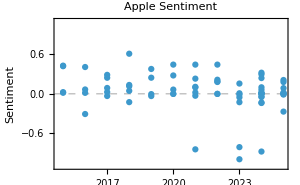
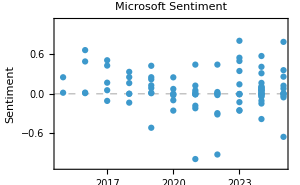
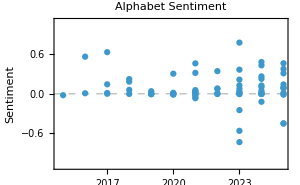
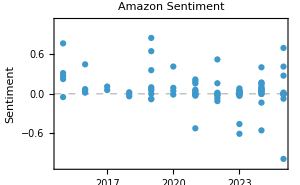
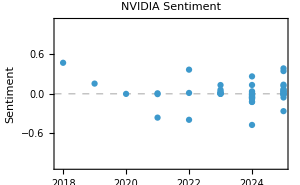
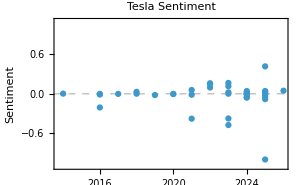
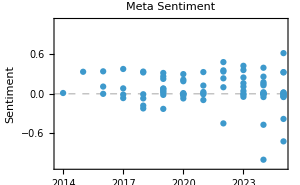
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

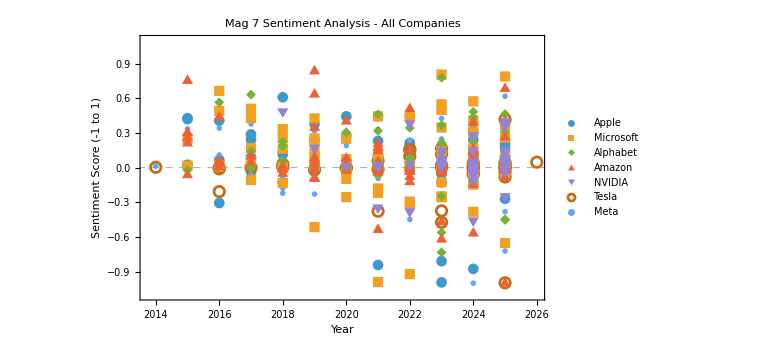

```mathematica
(* Import the JSON data *)
data = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];

(* Define the Mag 7 companies *)
companies = {"Apple", "Microsoft", "Alphabet", "Amazon", "NVIDIA", "Tesla", "Meta"};

(* Helper: Ensure we have an Association *)
toAssociation[obj_] := If[AssociationQ[obj], obj, Association[obj]];

(* Function to extract all entries with notes and initiatives from a company *)
extractEntries[companyRaw_] := Module[
  {companyData, allEntries = {}},
  
  companyData = toAssociation[companyRaw];
  
  Do[
    (* Iterate over categories (keys) *)
    If[ListQ[companyData[category]],
      allEntries = Join[allEntries, companyData[category]]
    ],
    {category, Keys[companyData]}
  ];
  
  allEntries
];

(* Function to combine notes and initiatives text *)
combineText[entry_] := Module[{notesText, initiativesText},
  notesText = If[KeyExistsQ[entry, "notes"] && StringQ[entry["notes"]], 
    entry["notes"], ""];
  initiativesText = If[KeyExistsQ[entry, "initiatives"] && ListQ[entry["initiatives"]], 
    StringRiffle[entry["initiatives"], " "], ""];
  StringTrim[notesText <> " " <> initiativesText]
];

(* Sentiment analyzer using built-in classifier *)
sentimentClassifier = Classify["Sentiment"];

(* Function to get numerical sentiment score from -1 to 1 *)
getSentiment[text_String] := Module[{probs, posScore, negScore},
  If[StringLength[text] == 0, Return[0]];
  probs = sentimentClassifier[text, "Probabilities"];
  posScore = Lookup[probs, "Positive", 0];
  negScore = Lookup[probs, "Negative", 0];
  (* Convert to -1 to 1 scale *)
  posScore - negScore
];

(* Process all companies and create sentiment data *)
companyData = Association[];

Do[
  Module[{entries, sentimentData},
    Print["Processing ", company, "..."];
    
    (* Safe Extraction *)
    If[KeyExistsQ[data, company],
      entries = extractEntries[data[company]];
      
      sentimentData = ParallelMap[
        Module[{year, text, sentiment},
          year = If[KeyExistsQ[#, "year"] && NumericQ[#["year"]], #["year"], Missing[]];
          text = combineText[#];
          sentiment = If[StringLength[text] > 0, getSentiment[text], Missing[]];
          <|"year" -> year, "sentiment" -> sentiment, "text" -> text|>
        ] &,
        entries
      ];
      
      (* Filter out entries with missing year or sentiment *)
      sentimentData = Select[sentimentData, 
        !MissingQ[#["year"]] && !MissingQ[#["sentiment"]] &];
      
      companyData[company] = sentimentData;
    ,
      Print["No data found for ", company];
      companyData[company] = {};
    ];
  ],
  {company, companies}
];

(* Create individual scatterplots for each company *)
plots = Table[
  Module[{compData, points},
    compData = companyData[company];
    If[Length[compData] == 0,
      Graphics[{Text[Style["No data available", 14], {0, 0}]}, Frame -> True, PlotLabel -> company],
      points = {#["year"], #["sentiment"]} & /@ compData;
      ListPlot[points,
        PlotLabel -> Style[company <> " Sentiment", 14, Bold],
        PlotRange -> {All, {-1.1, 1.1}},
        PlotStyle -> PointSize[0.015],
        GridLines -> {None, {0}},
        GridLinesStyle -> Directive[Gray, Dashed],
        Frame -> True,
        FrameLabel -> {None, "Sentiment"},
        ImageSize -> 300
      ]
    ]
  ],
  {company, companies}
];

(* Display all plots in a grid *)
Grid[Partition[plots, 3, 3, 1, {}], Spacings -> {1, 1}]

(* Create a combined plot with all companies *)
combinedPlot = Module[{allData, legendColors},
  allData = Table[
    Module[{compData, points},
      compData = companyData[company];
      If[Length[compData] > 0,
        points = {#["year"], #["sentiment"]} & /@ compData;
        {points, company},
        Nothing
      ]
    ],
    {company, companies}
  ];
  
  If[Length[allData] > 0,
    ListPlot[
      allData[[All, 1]],
      PlotLabel -> Style["Mag 7 Sentiment Analysis - All Companies", 18, Bold],
      PlotRange -> {All, {-1.1, 1.1}},
      GridLines -> {None, {0}},
      GridLinesStyle -> Directive[Gray, Dashed],
      Frame -> True,
      FrameLabel -> {"Year", "Sentiment Score (-1 to 1)"},
      PlotLegends -> Placed[allData[[All, 2]], Right],
      ImageSize -> Large,
      PlotMarkers -> Automatic
    ],
    "No data to plot."
  ]
]
```

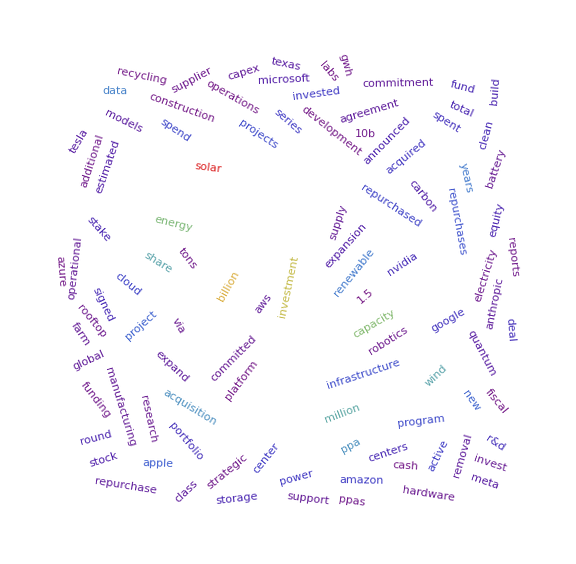

```mathematica
(* Import data *)
data = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];

(* Collect all text from notes and initiatives *)
allText = "";

Do[
  companyData = data[company];
  Do[
    entries = companyData[category];
    If[ListQ[entries],
      Do[
        (* Add notes *)
        If[KeyExistsQ[entry, "notes"] && StringQ[entry["notes"]],
          allText = allText <> " " <> entry["notes"]
        ];
        (* Add initiatives *)
        If[KeyExistsQ[entry, "initiatives"] && ListQ[entry["initiatives"]],
          allText = allText <> " " <> StringRiffle[entry["initiatives"], " "]
        ];
        (* Add source_figure *)
        If[KeyExistsQ[entry, "source_figure"] && StringQ[entry["source_figure"]],
          allText = allText <> " " <> entry["source_figure"]
        ],
        {entry, entries}
      ]
    ],
    {category, Keys[companyData]}
  ],
  {company, Keys[data]}
];

(* Clean text: remove stopwords and tokenize *)
words = DeleteStopwords[ToLowerCase[TextWords[allText]]];

(* Additional filtering: remove numbers, very short words, and common tech abbreviations *)
words = Select[words, 
  StringLength[#] > 2 && !StringMatchQ[#, DigitCharacter..] &
];

(* Count word frequencies *)
wordCounts = Reverse[SortBy[Tally[words], Last]];

(* Create WordCloud *)
WordCloud[
  wordCounts,
  ImageSize -> Large,
  ColorFunction -> "Rainbow",
  WordOrientation -> "Random"
]
```

---
## Source Domains Ordered By Prevelence

```mathematica
(* Import data *)
data = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];

(* Extract domain from a URL *)
extractDomain[url_String] := Module[{parsed},
  parsed = URLParse[url];
  Lookup[parsed, "Domain", "Unknown"]
];

(* Collect all URLs from the JSON *)
allURLs = {};

Do[
  companyData = data[company];
  Do[
    entries = companyData[category];
    If[ListQ[entries],
      Do[
        (* Check for "links" field (list of URLs) *)
        If[KeyExistsQ[entry, "links"] && ListQ[entry["links"]],
          allURLs = Join[allURLs, entry["links"]]
        ];
        (* Check for "source_url" field (single URL) *)
        If[KeyExistsQ[entry, "source_url"] && StringQ[entry["source_url"]],
          AppendTo[allURLs, entry["source_url"]]
        ],
        {entry, entries}
      ]
    ],
    {category, Keys[companyData]}
  ],
  {company, Keys[data]}
];

(* Extract domains and count *)
domains = extractDomain /@ allURLs;
domainCounts = Reverse[SortBy[Tally[domains], Last]];

(* Display in Grid: white rows with black text *)
Grid[
  Prepend[
    domainCounts,
    {Style["Domain", Bold, White, 14], Style["Citations", Bold, White, 14]}
  ],
  Frame -> All,
  Background -> { {Black}, Table[White, {Length[domainCounts]}] },   (* Black header, all white data rows *)
  Alignment -> {Left, Center},
  Dividers -> {None, {2 -> Thick}},
  ItemStyle -> { {Black}, Table[Black, {Length[domainCounts]}] }     (* Black text for all data rows *)
]
```

Domain | Citations
www.reuters.com | 61
financecharts.com | 45
www.apple.com | 35
news.microsoft.com | 32
www.aboutamazon.com | 21
press.aboutamazon.com | 20
blogs.microsoft.com | 18
techcrunch.com | 13
nvidianews.nvidia.com | 13
blog.google | 13
www.cnbc.com | 11
www.bloomberg.com | 11
www.theverge.com | 9
www.sec.gov | 7
aws.amazon.com | 7
www.tesla.com | 6
www.teslarati.com | 5
www.prnewswire.com | 5
www.geekwire.com | 5
www.apexcleanenergy.com | 5
electrek.co | 5
sustainability.fb.com | 4
sustainability.atmeta.com | 4
fortune.com | 4
engineering.fb.com | 4
developer.nvidia.com | 4
abc.xyz | 4
www.rwe.com | 3
www.redwoodmaterials.com | 3
www.power-technology.com | 3
www.pnm.com | 3
www.microsoft.com | 3
www.ft.com | 3
www.edpr.com | 3
waymo.com | 3
variety.com | 3
sustainability.google | 3
investor.fb.com | 3
esgtoday.com | 3
ec.europa.eu | 3
blogs.nvidia.com | 3
balkangreenenergynews.com | 3
arxiv.org | 3
ai.meta.com | 3
zelestra.energy | 2
www.utilitydive.com | 2
www.tva.com | 2
www.talenenergy.com | 2
www.smartenergydecisions.com | 2
www.shacknews.com | 2
www.rplusenergies.com | 2
www.nvidia.com | 2
www.macrumors.com | 2
www.macrotrends.net | 2
www.fool.com | 2
www.datacenterdynamics.com | 2
www.cybersecuritydive.com | 2
www.businesswire.com | 2
www.blog.google | 2
www.bbc.com | 2
www.about.fb.com | 2
www.aboutamazon.eu | 2
us.orsted.com | 2
tracxn.com | 2
renewablesnow.com | 2
machinelearning.apple.com | 2
macdailynews.com | 2
investor.firstsolar.com | 2
invenergy.com | 2
images.nvidia.com | 2
europa.eu | 2
esgnews.com | 2
datacenters.atmeta.com | 2
calcalistech.com | 2
apnews.com | 2
www.wsj.com | 1
www.twobirds.com | 1
www.tradewindenergy.com | 1
www.tipranks.com | 1
www.theinformation.com | 1
www.theguardian.com | 1
www.texasmonthly.com | 1
www.taipeitimes.com | 1
www.statista.com | 1
www.srpnet.com | 1
www.spinquanta.com | 1
www.siliconranch.com | 1
www.roadtoautonomy.com | 1
www.repsol.com | 1
www.rangerpower.com | 1
www.q4cdn.com | 1
www.originenergy.com.au | 1
www.nytimes.com | 1
www.nature.com | 1
www.nasdaq.com | 1
www.matthewball.co | 1
www.luxcara.com | 1
www.leveltenenergy.com | 1
www.invenergy.com | 1
www.ibvogt.com | 1
www.iberdrola.com | 1
www.heirloomcarbon.com | 1
www.globenewswire.com | 1
www.ftc.gov | 1
www.freightwaves.com | 1
www.forbes.com | 1
www.fiercehealthcare.com | 1
www.entrepreneur.com | 1
www.engie-sem.com | 1
www.engie.com | 1
www.energylivenews.com | 1
www.eenewseurope.com | 1
www.edf-re.uk | 1
www.diabetes.co.uk | 1
www.crn.com | 1
www.computerweekly.com | 1
www.businessofapps.com | 1
www.businessinsider.com | 1
www.avangrid.com | 1
www.anthropic.com | 1
www.ainvest.com | 1
www.aes.com | 1
www.aboutamazon.sg | 1
www.aboutamazon.in | 1
www.1pointfive.com | 1
venturebeat.com | 1
thequantuminsider.com | 1
techhq.com | 1
sustainabilitymag.com | 1
subtelforum.com | 1
seekingalpha.com | 1
sbenergy.com | 1
research.google | 1
renewablewatch.in | 1
pv-magazine-usa.com | 1
procurementpro.com | 1
news.dominionenergy.com | 1
mlq.ai | 1
markets.financialcontent.com | 1
issgovernance.com | 1
investors.catenaa.com | 1
humanprogress.org | 1
huggingface.co | 1
group14technologies.com | 1
gi-review.com | 1
geekwire.com | 1
finance.yahoo.com | 1
esgdive.com | 1
energynow.com | 1
energyconnects.com | 1
dig.watch | 1
digitalmusicnews.com | 1
datacenters.google | 1
crunchbase.com | 1
cloud.google.com | 1
cleantechnica.com | 1
carboncredits.com | 1
brookfield.com | 1
blog.whatsapp.com | 1
bep.brookfield.com | 1
bebeez.eu | 1
assets.aboutamazon.com | 1
arevonenergy.com | 1
apexcleanenergy.com | 1
analyzify.com | 1
advanced-television.com | 1
about.fb.com | 1
aboutamazon.com | 1

---
## Regression & ML
-   Predict market cap change% with features R&D spending, capex spending, renewable energy investment, M&A spending, PPA spending, opex spending, energy metrics, & emissions.
-   Model with OLS regression

```mathematica
(* Import all datasets *)
spendingData = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/mag7_spending.json", "RawJSON"];
marketData = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/market_valuation.json", "RawJSON"];
esgData = Import["https://raw.githubusercontent.com/shlinkLFO/Mag7/refs/heads/main/ESG.json", "RawJSON"];

companies = {"Alphabet", "Amazon", "Apple", "Meta", "Microsoft", "NVIDIA", "Tesla"};
years = Range[2020, 2024];

(* === Extract Annual Spending by Type === *)
getSpendingByTypeYear[company_, spendType_, year_] := Module[
  {compData, total = 0.0},
  compData = spendingData[company];
  Do[
    entries = compData[category];
    If[ListQ[entries],
      Do[
        If[ToLowerCase[Lookup[entry, "spend_type", ""]] == spendType &&
           Lookup[entry, "year", Null] == year,
          amount = Lookup[entry, "investment_amount_billions_usd", 0.0];
          If[NumericQ[amount], total += amount]
        ],
        {entry, entries}
      ]
    ],
    {category, Keys[compData]}
  ];
  total
];

(* === Extract Renewable/PPA Spending === *)
getRenewableSpending[company_, year_] := Module[
  {compData, total = 0.0},
  compData = spendingData[company];
  Do[
    entries = compData[category];
    If[ListQ[entries],
      Do[
        entryYear = Lookup[entry, "year", Null];
        spendType = ToLowerCase[Lookup[entry, "spend_type", ""]];
        entryType = ToLowerCase[Lookup[entry, "type", ""]];
        
        If[(StringContainsQ[category, "renewable"] || 
            StringContainsQ[entryType, "renewable"] ||
            spendType == "ppa") && entryYear == year,
          amount = Lookup[entry, "investment_amount_billions_usd", 0.0];
          If[NumericQ[amount], total += amount]
        ],
        {entry, entries}
      ]
    ],
    {category, Keys[compData]}
  ];
  total
];

(* === Extract Market Cap for Year (Q4) === *)
getMarketCap[company_, year_] := Module[{records, filtered},
  records = marketData["records"];
  filtered = Select[records, 
    #["company"] == company && #["fiscal_year"] == year && #["fiscal_quarter"] == "Q4" &];
  If[Length[filtered] > 0, filtered[[1]]["market_cap_usd"], Missing[]]
];

(* === Extract ESG Metrics === *)
getESGMetric[company_, year_, category_, field_] := Module[
  {compData, yearData, val},
  If[!KeyExistsQ[esgData["companies"], company], Return[Missing[]]];
  compData = esgData["companies"][company];
  If[!KeyExistsQ[compData, ToString[year]], Return[Missing[]]];
  yearData = First[compData[ToString[year]], <||>];
  If[!AssociationQ[yearData], Return[Missing[]]];
  If[!KeyExistsQ[yearData, category], Return[Missing[]]];
  val = Lookup[yearData[category], field, Missing[]];
  If[NumericQ[val], val, Missing[]]
];

(* === BUILD DATASET === *)
dataRows = {};

Do[
  Do[
    (* Get Market Cap for current and previous year *)
    mcCurrent = getMarketCap[company, year];
    mcPrevious = getMarketCap[company, year - 1];
    
    (* Calculate Market Cap Change % *)
    If[NumericQ[mcCurrent] && NumericQ[mcPrevious] && mcPrevious > 0,
      mcChange = 100 * (mcCurrent - mcPrevious) / mcPrevious;
      
      (* Extract features *)
      capex = getSpendingByTypeYear[company, "capex", year];
      opex = getSpendingByTypeYear[company, "opex", year];
      ppa = getSpendingByTypeYear[company, "ppa", year];
      ma = getSpendingByTypeYear[company, "m&a", year];
      equity = getSpendingByTypeYear[company, "equity", year];
      renewable = getRenewableSpending[company, year];
      
      (* ESG metrics *)
      energyMWh = getESGMetric[company, year, "energy_consumption", "total_consumption_mwh"];
      scope1 = getESGMetric[company, year, "emissions_mtco2e", "scope_1"];
      scope2 = getESGMetric[company, year, "emissions_mtco2e", "scope_2_market_based"];
      scope3 = getESGMetric[company, year, "emissions_mtco2e", "scope_3_total"];
      
      (* Convert missing ESG to 0 for regression *)
      energyGWh = If[NumericQ[energyMWh], energyMWh / 1000, 0.0];
      scope1Val = If[NumericQ[scope1], scope1 / 1000000, 0.0]; (* Convert to millions *)
      scope2Val = If[NumericQ[scope2], scope2 / 1000000, 0.0];
      scope3Val = If[NumericQ[scope3], scope3 / 1000000, 0.0];
      
      (* Add row if we have meaningful spending data *)
      If[capex + opex + ppa + ma + renewable > 0,
        AppendTo[dataRows, <|
          "Company" -> company,
          "Year" -> year,
          "MarketCapChange" -> mcChange,
          "Capex" -> capex,
          "Opex" -> opex,
          "PPA" -> ppa,
          "MA" -> ma,
          "Equity" -> equity,
          "Renewable" -> renewable,
          "EnergyGWh" -> energyGWh,
          "Scope1M" -> scope1Val,
          "Scope2M" -> scope2Val,
          "Scope3M" -> scope3Val
        |>]
      ]
    ],
    {year, years}
  ],
  {company, companies}
];

Print["Dataset rows: ", Length[dataRows]];

(* === PREPARE FOR REGRESSION === *)
(* Dependent Variable: Market Cap Change % *)
(* Independent Variables: Spending & ESG features *)

If[Length[dataRows] > 5,
  (* Extract vectors *)
  y = #["MarketCapChange"] & /@ dataRows;
  X = {
    #["Capex"],
    #["Opex"], 
    #["PPA"],
    #["MA"],
    #["Renewable"],
    #["EnergyGWh"],
    #["Scope3M"]
  } & /@ dataRows;
  
  featureNames = {"Capex", "Opex", "PPA", "M&A", "Renewable", "Energy(GWh)", "Scope3(M)"};
  
  (* Run OLS Regression *)
  model = LinearModelFit[Transpose[{Sequence @@ Transpose[X], y}], 
    {1, x1, x2, x3, x4, x5, x6, x7}, 
    {x1, x2, x3, x4, x5, x6, x7}];
  
  (* Display Results *)
  Print["\n=== OLS Regression Results ==="];
  Print["DV: Market Cap Change (%)"];
  Print["Observations: ", Length[y]];
  Print["\nR-Squared: ", model["RSquared"]];
  Print["Adjusted R-Squared: ", model["AdjustedRSquared"]];
  
  (* Coefficient Table *)
  coeffs = model["BestFitParameters"];
  pvals = model["ParameterPValues"];
  
  Print["\n=== Coefficients ==="];
  Grid[
    Prepend[
      Table[{
        If[i == 1, "Intercept", featureNames[[i - 1]]],
        NumberForm[coeffs[[i]], {5, 3}],
        NumberForm[pvals[[i]], {5, 4}],
        If[pvals[[i]] < 0.01, "***", If[pvals[[i]] < 0.05, "**", If[pvals[[i]] < 0.1, "*", ""]]]
      }, {i, Length[coeffs]}],
      {Style["Variable", Bold], Style["Coefficient", Bold], Style["P-Value", Bold], Style["Sig.", Bold]}
    ],
    Frame -> All,
    Alignment -> {Left, Center}
  ],
  
  Print["Insufficient data for regression. Found only ", Length[dataRows], " complete observations."]
]
```

Dataset rows: 19

=== OLS Regression Results ===

DV: Market Cap Change (%)

Observations: 19

R-Squared: 0.394069

Adjusted R-Squared: 0.00847722

=== Coefficients ===

Variable | Coefficient | P-Value | Sig.
Intercept | 57.780 | 0.0140 | **
Capex | 1.846 | 0.0628 | *
Opex | -0.098 | 0.3694 | 
PPA | -4.224 | 0.9320 | 
M&A | -5.693 | 0.1598 | 
Renewable | 1.674 | 0.9730 | 
Energy(GWh) | -0.001 | 0.3463 | 
Scope3(M) | -0.048 | 0.9426 |

---
## Results & Conclusions

#### How much does each of the Magnificent 7 spend on each type of expenditure? - Each of the Mag 7 spend the most on equity expenditure except for Amazon who spends the most on capex expenditure. - More opex expenditure was found for Meta, Alphabet, & NVIDIA than capex - Microsoft & Apple's expenditure on opex and capex summed to about the same amount - More capex expenditure was found for Tesla & Amazon than opex - Microsoft's M&A expenditure was summed to be the largest of the 7 - Apple, NVIDIA, & Tesla spend almost nothing on PPA's #### How much does the Magnificent 7 spend on their domains of focus? - Apple spends the most on Digital Inclusion & Economy, and Share Repurchases - Microsoft spends the most on Share Repurchases, Content Production Studios, and AI Foundation Models - Alphabet spends the most on Share Repurchases, Autonomous Mobility, Mergers & Acquisitions - Amazon spends the most on Cloud Data Centers & AI Infra, Content Production Studios, and Industrial Automation Supply Chain - Meta spends the most on Share Repurchases, and XR Metaverse & Spatial Computing - NVIDIA spends the most on Share Repurchases, AI Foundation Models - Tesla spends the most on Autonomous Mobility #### How comitted is each of the Magnificent 7 to *renewable energy sourcing*? - Tesla and Microsoft have Renewable Investment Ratio's (CapEx and OpEx Expenditures [PPA's were split] on Renewable Energy Generation divided by the term length of the contract to get yearly expenditure) were found to be the best of the Mag 7, boasting 5 times more expenditure on renewable energy than the cost of electricity in 2024. - Apple's ratio was also above 1, sitting at about 1.5 for 2024. - Meta score 0.8 and Alphabet 0.6 - Amazon scored the worst with a score of 0.4 - *Renewable energy expenditure announcements are scarce, and company guidance reports can be deceitful (renewable energy sourcing at Amazon is 100% despite high Scope 2 Emissions)* #### How much energy does each of the Magnificent 7 report consuming? - In 2022, Amazon cossumed the most energy, reporting ~30,000 GWh. Google & Microsoft consumed about 20,000 GWh, Meta ~11,000, & Apple, NVIDIA, and Tesla under 5,000 GWh - In 2024, Amazon consumed nearly 50,000 GWh. Google & Microsoft consumed about 25,000 GWh, Meta ~15,000, & Apple, NVIDIA, and Tesla remain under 5,000 GWh #### Where are each of the Magnificent 7's datacenters located? How much energy do they consume? - Most of the datacenters that consue the most energy are on the US East Coast, in the Midwest, in Texas, or on the Wesst Coast. There are a few medium sized locations in Europe, and sparse locations worldwide. #### Can market cap change% be modeled using OLS Regression with features R&D spending, capex spending, renewable energy investment, M&A spending, PPA spending, opex spending, energy metrics, & emissions with precision? - No. Adjusted R-Squared was found to be 0.00847722 and capex expenditure was the only slightly statistically significant predictor with a p-value of 0.0628